# clonal-hem-notebook.nb

## Mathematical analysis and data presentation functions

Author: Peter Ashcroft, ETH Zürich

```mathematica
(*Clear output cells before saving and pushing!*)
NotebookDelete[Cells[EvaluationNotebook[],CellStyle->{"Output"}] ];
```

```mathematica
(*Define plot style for this notebook. 
Run before evaluating notebook cells to avoid errors!*)
myPlotStyle={
col->§col,
sym->{
{Graphics@{§col[[1]],Circle[]},0.05},
{Graphics@{FaceForm[Opacity[0] ],EdgeForm[Directive[§col[[2]],Opacity[1] ] ],Rectangle[]},0.04},
{Graphics@{FaceForm[Opacity[0] ],EdgeForm[Directive[§col[[3]],Opacity[1] ] ],Polygon[{{0.5,0},{1,0.5},{0.5,1},{0,0.5}}]},0.06},
{Graphics@{FaceForm[Opacity[0] ],EdgeForm[Directive[§col[[4]],Opacity[1] ] ],Triangle[{{0,0},{1,0},{0.5,(√3)/2}}]},0.05}
},
symFull->{
{Graphics@{§col[[1]],Disk[]},0.05},
{Graphics@{FaceForm[Directive[§col[[2]],Opacity[1] ] ],EdgeForm[Opacity[0] ],Rectangle[]},0.04},
{Graphics@{FaceForm[Directive[§col[[3]],Opacity[1] ] ],EdgeForm[Opacity[0] ],Polygon[{{0.5,0},{1,0.5},{0.5,1},{0,0.5}}]},0.06},
{Graphics@{FaceForm[Directive[§col[[4]],Opacity[1] ] ],EdgeForm[Opacity[0] ],Triangle[{{0,0},{1,0},{0.5,(√3)/2}}]},0.05}
},
labelSize->22,
ticksSize->16,
insetSize->12,
font->"Helvetica"
}/.§col->{RGBColor[94/255,60/255,153/255],RGBColor[230/255,97/255,1/255],RGBColor[178/255,171/255,210/255],RGBColor[253/255,184/255,99/255]}//Quiet;

getTickLocations[{fmin_,fmax_}]:=Module[{series,min,max,tickLocations},
series=Table[N[Mod[i,9,1]×10^(Floor[i-1,9]/9)],{i,-89,91}];

min=Position[Map[#≤fmin&,series],True][[-1,1]];
max=FirstPosition[Map[#≥fmax&,series],True][[1]];

tickLocations=series[[min;;max]];

Return[tickLocations];
]
logTicks[{fmin_,fmax_},label_,sciFormat_]:=Module[{tickLocations,n ,power10,tickLabels,Δ=0.01,tickSizes,ticks},
tickLocations=getTickLocations[{fmin,fmax}];
n=Length[tickLocations];

power10=Map[MemberQ[Table[10.^i,{i,-10,10}],#]&,tickLocations];(*Is our location a power of 10?*)

tickLabels=If[label,
Table[If[power10[[i]],If[sciFormat,Superscript["10",Round[Log10[tickLocations[[i]] ] ] ],If[tickLocations[[i]]≥1,Round[tickLocations[[i]] ],tickLocations[[i]] ] ],""],{i,1,n}],
ConstantArray["",n]
];

tickSizes=Transpose[{Map[If[#,Δ,Δ/2]&,power10],ConstantArray[0,n]}];

ticks=Transpose[{tickLocations,tickLabels,tickSizes}];

Return[ticks];
]
```

## 1. Basic model: steady-state mouse parameters, residence times, and fluxes

### ρ=0, α=0

#### {δ, d, a}

```mathematica
params[§s_,§ℓ_]:={β n/s,s/(ℓ n)-β,(1/ℓ-(β n)/s)𝒩/(𝒩-n)}/.{𝒩->10000,β->1./39,n->9900,s->§s,ℓ->(§ℓ)/1440.}
paramTab[§s_]:=TableForm[Transpose[{params[§s,1],params[§s,3],params[§s,5]}],TableHeadings->{{"δ","d","a"},{"ℓ=1","ℓ=3","ℓ=5"}}]
```

```mathematica
paramTab[1]
```

```mathematica
paramTab[10]
```

```mathematica
paramTab[100]
```

#### Residence time in BM

```mathematica
resTime[§s_,§ℓ_]:={(s/(ℓ n)-β)^-1×24,(s/(ℓ n)-β)^-1}/.{𝒩->10000,β->1./39,n->9900,s->§s,ℓ->(§ℓ)/1440.}
resTimeTab[§s_]:=TableForm[Transpose[{resTime[§s,1],resTime[§s,3],resTime[§s,5]}],TableHeadings->{{"hours","days"},{"ℓ=1","ℓ=3","ℓ=5"}}]
```

```mathematica
resTimeTab[1]
```

```mathematica
resTimeTab[10]
```

```mathematica
resTimeTab[100]
```

#### Flux

```mathematica
flux[§s_,§ℓ_]:={s/ℓ,(d n+β n)/.d->s/(ℓ n)-β}/.{𝒩->10000,β->1./39,n->9900,s->§s,ℓ->(§ℓ)/1440.}
fluxTab[§s_]:=TableForm[Transpose[{flux[§s,1],flux[§s,3],flux[§s,5]}],TableHeadings->{{"flux out of PB","flux out of BM"},{"ℓ=1","ℓ=3","ℓ=5"}}]
```

```mathematica
fluxTab[1]
```

```mathematica
fluxTab[10]
```

```mathematica
fluxTab[100]
```

### ρ=0, α≠0

#### Alternative model: {δ, d, a}

```mathematica
params[§s_,§ℓ_,§α_]:={(β n)/(s+α n),s/(ℓ n)-β,(1/ℓ-(β n)/(s+α n))𝒩/(𝒩-n)}/.{𝒩->10000,β->1./39,n->9900,s->§s,ℓ->(§ℓ)/1440.,α->§α}
paramTab[§s_,§αVals_]:=TableForm[Transpose[Table[params[§s,3,§α],{§α,§αVals}] ],TableHeadings->{{"δ","d","a"},Table[If[§α==0,"α="<>ToString[§α],Superscript["α=10",Log10[§α] ] ],{§α,§αVals}]}]
```

```mathematica
αVals={0,10^-4,10^-2,1};
```

```mathematica
paramTab[1,αVals]
```

```mathematica
paramTab[100,αVals]
```

### ρ=ρ_0(N-n)/N, α≠0

#### Find parameters in terms of knowns

```mathematica
Solve[{0==(d+β(1-ρ (𝒩-n)/𝒩))n-(a (𝒩-n)/𝒩+δ)s,0==(β ρ (𝒩-n)/𝒩-d-α δ)n+a s (𝒩-n)/𝒩,ℓ==1/(δ+a (𝒩-n)/𝒩)},{δ,d,a}]
```

#### {δ, d, a}

```mathematica
params[§s_,§ℓ_,§α_]:={β n/(s+α n),s/(ℓ n)-β(1-ρ (𝒩-n)/𝒩),(1/ℓ-(β n)/(s+α n))𝒩/(𝒩-n)}/.{𝒩->10000,β->1./39,n->9900,s->§s,ℓ->(§ℓ)/1440.,α->§α}
paramTab[§s_,§αVals_]:=TableForm[Transpose[Table[params[§s,3,§α],{§α,§αVals}] ],TableHeadings->{{"δ","d","a"},Table[If[§α==0,"α="<>ToString[§α],Superscript["α=10",Log10[§α] ] ],{§α,§αVals}]}]
```

```mathematica
αVals={0,10^-4,10^-2,1};
```

```mathematica
paramTab[1,αVals]
```

```mathematica
paramTab[100,αVals]
```

### ρ=ρ_0(N-n)/(N-n^×), α≠0 (Also for step function, ρ(n)=ρ_0 δ_(n,N))

#### Find parameters in terms of knowns

```mathematica
Solve[{0==(d+β(1-ρ ))n-(a (𝒩-n)/𝒩+δ)s,0==(β ρ-d-α δ)n+a s (𝒩-n)/𝒩,ℓ==1/(δ+a (𝒩-n)/𝒩)},{δ,d,a}]
```

#### {δ, d, a}

```mathematica
params[§s_,§ℓ_,§α_]:={β n/(s+α n),s/(ℓ n)-β(1-ρ ),(1/ℓ-(β n)/(s+α n))𝒩/(𝒩-n)}/.{𝒩->10000,β->1./39,n->9900,s->§s,ℓ->(§ℓ)/1440.,α->§α}
paramTab[§s_,§αVals_]:=TableForm[Transpose[Table[params[§s,3,§α],{§α,§αVals}] ],TableHeadings->{{"δ","d","a"},Table[If[§α==0,"α="<>ToString[§α],Superscript["α=10",Log10[§α] ] ],{§α,§αVals}]}]
```

```mathematica
αVals={0,10^-4,10^-2,1};
```

```mathematica
paramTab[1,αVals]
```

```mathematica
paramTab[100,αVals]
```

## 2. Mathematical analysis of time to clonality (ρ=α=0)

## Neutral clone

### Jacobian and eigensystem

Writing x⃗=(s_1,s_2,n_1,n_2)/N, the neutral ODEs for dx⃗/dt are given by:

```mathematica
odes={
(d+β)x3-(δ+a(1-x3-x4)) x1 ,
(d+β)x4-(δ+a(1-x3-x4)) x2,
-d x3+a(1-x3-x4)x1,
-d x4+a (1-x3-x4)x2
};
```

The slow manifold is given by xStar. We then compute the Jacobian of the ODEs about this point.

```mathematica
xStar=({x1->β/δ(ξ-z),x2->β/δ z,x3->(ξ-z),x4->z}/.ξ->1-(d δ)/(a β));
J=FullSimplify[D[odes,{{x1,x2,x3,x4}}]/.xStar];
MatrixForm[J]
```

Now we compute the eigenvalues, and right & left eigenvectors of J.

```mathematica
λ=FullSimplify[Eigenvalues[J],Assumptions->{a>0,d>0,δ>0,β>0,z>0}]
```

```mathematica
v=FullSimplify[Eigenvectors[J],Assumptions->{a>0,d>0,δ>0,β>0,z>0}]
```

```mathematica
u=FullSimplify[Eigenvectors[Transpose[J]],Assumptions->{a>0,d>0,δ>0,β>0,z>0}]
```

Here we extract the first eigenvectors, corresponding to the zero eigenvalue. They are rescaled so that they look pretty and so that v1·u1=1.

```mathematica
v1=FullSimplify[v[[1]]/v[[1,4]]]
u1=FullSimplify[u[[1]]/(u[[1]].v1)]
Simplify[v1.u1]
```

### Diffusion matrix

By considering the individual-based reactions, we can construct multiplicative diffusion matrix for the SDE approximation.
We can then evaluate this on the slow-manifold xStar.

```mathematica
B={
{(d+β)x3 +(δ+a(1-x3-x4))x1,0,-d x3-a(1-x3-x4)x1,0},
{0,(d+β)x4 +(δ+a(1-x3-x4))x2,0,-d x4-a(1-x3-x4)x2},
{-d x3-a(1-x3-x4)x1,0,d x3+a(1-x3-x4)x1,0},
{0,-d x4-a(1-x3-x4)x2,0,d x4+a(1-x3-x4)x2}
};
```

```mathematica
B=FullSimplify[B/.xStar];
MatrixForm[B]
```

New diffusion coefficient, which is the diffusion matrix projected onto the slow-manifold direction using the leading left eigenvector.

```mathematica
Simplify[u1.(B.u1)]
```

Let’s write that in a neater form.

```mathematica
BTilde=(2 d (d+β)β δ^2)/(ξ(β δ+β d+d δ)^2)z(ξ-z)/.ξ->1-(d δ)/(a β);
```

```mathematica
(*Check*)
FullSimplify[u1.(B.u1)-BTilde]
```

The coefficient, which we write as ℬ in the manuscript, can be expressed in terms of the fundamental parameters (β,𝒩,s,n,ℓ).

```mathematica
paramSub={δ->(β n)/s,d->(1/ℓ s)/n-β,a->(1/ℓ-(β n)/s)𝒩/(𝒩-n)};
FullSimplify[(a d (d+β)β^2 δ^2)/((a β-d δ)(β δ+d(β+δ))^2)/.paramSub]
```

### Fixation probability and times

We start the process on the slow manifold at the position z0. We want to know what is the probability our mutant reaches fixation (z=ξ), and how long this takes.

```mathematica
assumptions={0≤z≤ξ,0<ξ<1,𝒩>0,ℬ>0};
```

```mathematica
(*Fixation probability*)
DSolve[{ϕ''[z]==0,ϕ[0]==0,ϕ[ξ]==1},ϕ[z],z]//First
```

```mathematica
(*Mean unconditional fixation time*)
Simplify[DSolve[{t''[z]==-𝒩/(ℬ z(ξ-z)),t[0]==0,t[ξ]==0},t[z],z],Assumptions->assumptions]//First
```

```mathematica
(*Mean conditional fixation time*)
Simplify[DSolve[{θ''[z]==-𝒩/(ℬ z(ξ-z))z/ξ,θ[0]==0,θ[ξ]==0},θ[z],z],Assumptions->assumptions]//First;
Simplify[Subscript[t, ξ][z]->((θ[z]/.%)/(z/ξ)),Assumptions->assumptions]
```

```mathematica
(*Second moment: NEW!*)
Simplify[DSolve[{θ''[z]==-2 𝒩/(ℬ z(ξ-z))(z/ξ(𝒩 (ξ-z) Log[ξ/(ξ-z)])/(ℬ z)),θ[0]==0,θ[ξ]==0},θ[z],z,Assumptions->assumptions],Assumptions->assumptions]//First;
Simplify[Subscript[sec, ξ][z]->((θ[z]/.%)/(z/ξ)),Assumptions->assumptions]
```

```mathematica
(*Check with my simplified solution*)
FullSimplify[(Subscript[sec, ξ][z]/.%)-((2 𝒩^2)/ℬ^2 (((ξ-z)/z) Log[(ξ-z)/ξ]+(PolyLog[2,1]-PolyLog[2,z/ξ]) ) )]
```

### Fixation probability and times to σ-level of chimerism

If we want to know if our mutant reaches a given level of clonality/chimerism (σ), we need to modify the boundary conditions.

```mathematica
assumptions={0≤z≤ξ,0<ξ<1,𝒩>0,ℬ>0,0<σ≤1};
```

```mathematica
(*Fixation Probability*)
Simplify[DSolve[{ϕ''[z]==0,ϕ[0]==0,ϕ[σ ξ]==1},ϕ[z],z],Assumptions->assumptions]//First
```

```mathematica
(*Mean unconditional fixation time *)
Simplify[DSolve[{ t''[z]==-𝒩/(ℬ z(ξ-z)),t[0]==0,t[σ ξ]==0},t[z],z,Assumptions->assumptions],Assumptions->assumptions]//First
```

```mathematica
(*Mean conditional fixation time*)
Simplify[DSolve[{ θ''[z]==-𝒩/(ℬ z(ξ-z))z/(σ ξ),θ[0]==0,θ[σ ξ]==0},θ[z],z,Assumptions->assumptions],Assumptions->assumptions]//First;
Simplify[Subscript[t, ξ][z]->((θ[z]/.%)/(z/(σ ξ))),Assumptions->assumptions]
```

```mathematica
(*Check my simplified form*)
FullSimplify[(Subscript[t, ξ][z]/.%)-(𝒩/ℬ((ξ-z)/z Log[ξ/(ξ-z)]+(1-σ)/σ Log[1-σ])),Assumptions->assumptions]
```

```mathematica
(*Second moment: NEW!*)
FullSimplify[DSolve[{θ''[z]==-2 𝒩/(ℬ z(ξ-z))(z/(σ ξ)𝒩/ℬ((ξ-z)/z Log[ξ/(ξ-z)]+1/σ(1-σ)Log[1-σ])),θ[0]==0,θ[ξ]==0},θ[z],z,Assumptions->assumptions],Assumptions->assumptions]//First
FullSimplify[Subscript[sec, ξ][z]->((θ[z]/.%)/(z/(σ ξ))),Assumptions->assumptions]
```

#### Manual calculation to avoid imaginary numbers

```mathematica
Clear[f]
```

```mathematica
(*Integrating the θ'' equation gives the following solution, from which we can determine the integration constants c1 and c2*)
f[z_]:=-2 𝒩^2/(ℬ^2 σ ξ)(-z-(ξ-z)Log[(ξ-z)/ξ]+z PolyLog[2,z/ξ]-1/σ(1-σ)Log[1-σ](ξ-z)(1-Log[ξ-z])+c1 z+c2)
c=Solve[{f[0]==0,f[σ ξ]==0},{c1,c2}]//First
```

```mathematica
FullSimplify[f[z]/.c]
```

```mathematica
(*Test with second moment of fixation time (σ=1)*)
```

```mathematica
FullSimplify[Limit[(f[z]/.c)/(z/(σ ξ)),σ->1]-((2 𝒩^2)/ℬ^2 (((ξ-z)/z) Log[(ξ-z)/ξ]+(PolyLog[2,1]-PolyLog[2,z/ξ]) ) )]
```

```mathematica
(*Check my simplified (rewritten) solution*)
```

```mathematica
gg=(2 𝒩^2)/ℬ^2 ((ξ-z)/z Log[(ξ-z)/ξ]+(PolyLog[2,σ]- PolyLog[2,z/ξ])+(1-σ)/σ Log[1-σ] ((ξ-z)/z Log[ξ/(ξ-z)]+(1-σ)/σ Log[1-σ]-1));
FullSimplify[(f[z]/.c)/(z/(σ ξ))-gg,Assumptions->assumptions]
```

## Advantageous clone

### Jacobian and eigensystem of neutral system

Writing x⃗=(s_1,s_2,n_1,n_2)/N, the neutral ODEs for dx⃗/dt are given by:

```mathematica
odesNeutral={
(d+β)x3-(δ+a(1-x3-x4)) x1 ,
(d+β)x4-(δ+a(1-x3-x4)) x2,
-d x3+a(1-x3-x4)x1,
-d x4+a (1-x3-x4)x2
};
```

The slow manifold is given by xStar. We then compute the Jacobian of the ODEs about this point.

```mathematica
xStar=({x1->β/δ(ξ-z),x2->β/δ z,x3->(ξ-z),x4->z}/.ξ->1-(d δ)/(a β));
J=FullSimplify[D[odesNeutral,{{x1,x2,x3,x4}}]/.xStar];
MatrixForm[J]
```

Now we compute the eigenvalues, and right & left eigenvectors of the neutral Jacobian, J.

```mathematica
λ=FullSimplify[Eigenvalues[J],Assumptions->{a>0,d>0,δ>0,β>0,z>0}]
```

```mathematica
vLong=FullSimplify[Eigenvectors[J],Assumptions->{a>0,d>0,δ>0,β>0,z>0}]
```

```mathematica
uLong=FullSimplify[Eigenvectors[Transpose[J]],Assumptions->{a>0,d>0,δ>0,β>0,z>0}]
```

For aesthetics, we make sure z does not appear in the denominator. We also normalise the left eigenvectors.

```mathematica
vNorm=FullSimplify[{vLong[[1]]/vLong[[1,4]],vLong[[2]]/vLong[[2,4]],z vLong[[3]]/vLong[[3,4]],z vLong[[4]]/vLong[[4,4]]}]
```

```mathematica
uNorm=FullSimplify[Table[uLong[[i]]/(uLong[[i]].vNorm[[i]]),{i,1,4}]]
```

The eigenvectors can be compactified further by expressing them in terms of the eigenvalues.
Here we check that our shortened forms fit with the solutions above, and that they are orthonormal.

```mathematica
v={
{-β/δ,β/δ,-1,1},
{(β+d)/d,-(β+d)/d,-1,1},
{(β-λ[[3]])/(δ+λ[[3]])(ξ-z),β/(d δ)(λ[[3]]+(a β)/δ)z,(ξ-z),z},
{(β-λ[[4]])/(δ+λ[[4]])(ξ-z),β/(d δ)(λ[[4]]+(a β)/δ)z,(ξ-z),z}
}/.ξ->1-(d δ)/(a β);
u={
(a β δ)/((a β-d δ) (β δ+d (β+δ))){-d z,d(ξ- z),-(β+d)z,(β+d)(ξ-z)},
(a d β)/((a β-d δ) (β δ+d (β+δ))){δ z,-δ(ξ- z),-β z,β(ξ-z)},
a/(2(a β-d δ) (λ[[3]]+(a β)/(2δ)+((β+d)δ)/(2β))){d δ,d δ,β(λ[[3]]+(β+d)/β δ),β(λ[[3]]+(β+d)/β δ)},
a/(2(a β-d δ)(λ[[4]]+(a β)/(2δ)+((β+d)δ)/(2β))){d δ,d δ,β(λ[[4]]+(β+d)/β δ),β(λ[[4]]+(β+d)/β δ)}
}/.ξ->1-(d δ)/(a β);
```

```mathematica
FullSimplify[vNorm-v]
FullSimplify[uNorm-u]
```

```mathematica
Table[FullSimplify[u[[i]].v[[j]]],{i,1,4},{j,1,4}]
```

### Drift vector

We find that the new drift vector along the slow-subspace satisfies ϵ u1.h, where h is the extra drift on the slow-manifold xStar due to the selective effect of ϵ.

```mathematica
h=Simplify[{0,(d γd+β γβ)x4-(δ γδ+a γa(1-x3-x4))x2,0,-d γd x4 + a γa(1-x3-x4)x2}/.xStar];
```

```mathematica
FullSimplify[ϵ u[[1]].h]
```

Again this can be written in a more compact form (as 𝒜 z(ξ-z)).

```mathematica
FullSimplify[(ϵ u[[1]].h)-(ϵ(a d β^2 δ)/((a β-d δ)(d β+d δ+β δ))((γβ-γδ)-(γd-γa))z(ξ-z))/.ξ->1-(d δ)/(a β)]
```

### Slow subspace

Our slow-subspace satisfies the form x̃=x^*+ϵ f(z), where f(z) is given by:

```mathematica
f=FullSimplify[Sum[-1/λ[[k]](u[[k]].h)v[[k]],{k,2,4}]];
xTilde=FullSimplify[({x1,x2,x3,x4}/.xStar)+ϵ f]
```

#### Visualise slow subspace

```mathematica
(*ODE solver*)
solveODEs[params_,T_]:=Module[{paramSub,initialCondition,eqs,dSol},
paramSub={δ->(β nStar)/sStar,d->sStar/(ℓ nStar)-β,a->(1/ℓ-(β nStar)/sStar)𝒩/(𝒩-nStar)};

initialCondition={s1[0]==sStar,s2[0]==𝒮,n1[0]==nStar,n2[0]==0};

eqs=({
s1'[t]==(d1+β1)n1[t]-(δ1+a1(𝒩-n1[t]-n2[t])/𝒩)s1[t] ,
s2'[t]==(d2+β2)n2[t]-(δ2+a2(𝒩-n1[t]-n2[t])/𝒩)s2[t],
n1'[t]==-d1 n1[t]+a1(𝒩-n1[t]-n2[t])/𝒩 s1[t],
n2'[t]==-d2 n2[t]+a2(𝒩-n1[t]-n2[t])/𝒩 s2[t]
}/.{a1->a,d1->d,β1->β,δ1->δ,a2->(1+γa ϵ)a,d2->(1+γd ϵ)d,β2->(1+γβ ϵ)β,δ2->(1+γδ ϵ)δ})/.paramSub;

dSol=NDSolve[Flatten[{eqs/.params,initialCondition/.params}],{s1[t],s2[t],n1[t],n2[t]},{t,0,T}][[1]];
Return[dSol]
]
```

```mathematica
(*Plotting function*)
pPlot[i_,odeSols_,paramsTab_,T_]:=Module[{paramSub,xTilde,odeSols§i,paramsTab§i,nϵ,myCol,plot},
paramSub={δ->(β nStar)/sStar,d->sStar/(ℓ nStar)-β,a->(1/ℓ-(β nStar)/sStar)𝒩/(𝒩-nStar)};
xTilde={(β (1-z-(d δ)/(a β)-(d z β (a (-1+z) β+d δ) (a d β^2 (γβ-γδ)+β (d^2 (γa-γd)+a (d+β) (γa-γd+2 γβ-2 γδ)) δ+(d+β) (d (γa-γd)+a (γa-γd+γβ-γδ)) δ^2+(d+β) (γa-γd+γβ-γδ) δ^3) ϵ)/((a β-d δ)^2 (β δ+d (β+δ))^2)))/δ,(z β (1+((a d β δ (d^2 z β^2 (γa-γd)+d (2+z) β (d+β) (γa-γd) δ+(d+β) (2 d (γa-γd)+β (-2 γβ+z (γa-γd+γβ-γδ)+2 γδ)) δ^2)+a^2 β^2 (d^2 z β^2 (γβ-γδ)+d β (d+β) ((-1+z) γa+γd-z (γd-2 γβ+2 γδ)) δ+(d+β) (β (γβ-γδ)+d ((-1+z) γa+γd-z (γd-γβ+γδ))) δ^2)-d^2 (d+β) δ^3 (β (-γβ+γδ) δ+d (γa-γd) (β+δ))) ϵ)/((a β-d δ)^2 (β δ+d (β+δ))^2)))/δ,1-z-(d δ)/(a β)+(d z (a (-1+z) β+d δ) (δ (d^2 β^2 (-2 γa+2 γd-γβ+γδ)+d β (β (-2 γa+2 γd-γβ+γδ)+d (-3 γa+3 γd-2 γβ+2 γδ)) δ-(d+β)^2 (γa-γd+γβ-γδ) δ^2)+a β^2 (β (-γβ+γδ) δ+d (γa-γd) (β+δ))) ϵ)/((a β-d δ)^2 (β δ+d (β+δ))^2),(z ((β δ+d (β+δ))^2+d β (β (-γβ+γδ) δ+d (γa-γd) (β+δ)) ϵ+(a d z β (δ (d^2 β^2 (2 γa-2 γd+γβ-γδ)+d β (d (3 γa-3 γd+2 γβ-2 γδ)+β (2 γa-2 γd+γβ-γδ)) δ+(d+β)^2 (γa-γd+γβ-γδ) δ^2)+a β^2 (β (γβ-γδ) δ-d (γa-γd) (β+δ))) ϵ)/(a β-d δ)^2))/(β δ+d (β+δ))^2}/.paramSub;
odeSols§i=odeSols[[i]];
paramsTab§i=paramsTab[[i]];
nϵ=Length[paramsTab§i];

myCol=col/.myPlotStyle;

plot=Show[
ParametricPlot[Evaluate[Table[{s1[t],s2[t]}/.odeSols§i[[j]],{j,1,nϵ}]],{t,0,T},MaxRecursion->15,PlotStyle->Table[Directive[myCol[[j]]],{j,1,nϵ}],PlotRange->All ],
ParametricPlot[Evaluate[Table[((𝒩 (xTilde/.z->nStar/𝒩 x))/.paramsTab§i[[j]])[[{1,2}]],{j,1,nϵ}]],{x,0,1},PlotStyle->Table[Directive[myCol[[j]],Dashing[{0.02,0.02}],Thickness[0.01]],{j,1,nϵ}] ],


Graphics[{Opacity[0.2],Thickness[0.02],Arrowheads[0.1],Arrow[{Scaled[{0.1,0.3}],Scaled[{0.5,0.7}]}]}],
Graphics[Text[Style["ε",labelSize,FontFamily->font,GrayLevel[0.4]],Scaled[{0.54,0.74}]]],

PlotRange->{{0,(1+Max[ϵVals])× sStarVals[[i]]},{0,(1+Max[ϵVals])×sStarVals[[i]]}},
PlotRangePadding->0,

Frame->True,
FrameLabel->{{Style["s_2",labelSize,FontFamily->font],None},{Style["s_1",labelSize,FontFamily->font],Style["s^*="<>ToString[sStarVals[[i]]],labelSize,FontFamily->font]}},
FrameTicksStyle->Directive[ticksSize,FontFamily->font],


ImageSize->350,
ImagePadding->{{52,15},{45,30}},
AxesOrigin->{0,0}
]/.myPlotStyle;
Return[plot];
]
```

```mathematica
(*Determine parameters and evaluate trajectories from ODEs*)
sStarVals={10,100};
nS=Length[sStarVals];

ϵVals={0,0.1,0.5,1.5};
nϵ=Length[ϵVals];

paramsFunc[§sStar_,§ϵ_]:={𝒩->10000,sStar->§sStar,nStar->9900,β->1./39,𝒮->5000,ℓ->3/1440.,ϵ->§ϵ,γβ->1,γδ->0,γd->0,γa->0};
paramsTab=Table[Table[paramsFunc[sStarVals[[i]],ϵVals[[j]] ],{j,1,nϵ}],{i,1,nS}];

T=3000;
odeSols=Table[Table[solveODEs[paramsTab[[i,j]],T],{j,1,nϵ}],{i,1,nS}];
```

```mathematica
(*Plot*)
Row[Table[pPlot[i,odeSols,paramsTab,T],{i,1,nS}]]
```

### Diffusion matrix

We assume the diffusion coefficient is unchanged by selection, such that it is as described in the neutral case, i.e.

```mathematica
BTilde=(2a d (d+β)β^2 δ^2)/((a β-d δ)(β δ+d(β+δ))^2)z(ξ-z)/.ξ->1-(d δ)/(a β);
```

### Fixation probability and times

We start the process on the slow manifold at the position z0. We want to know what is the probability our mutant reaches fixation (z=ξ), and how long this takes.
We write Λ=ϵ 𝒩 𝒜/ℬ (const.).

```mathematica
assumptions={0≤z≤ξ,0<ξ<1,𝒩>0,ℬ>0,Λ>0};
```

```mathematica
(*Fixation Probability*)
Simplify[DSolve[{Λ ϕ'[z]+ϕ''[z]==0,ϕ[0]==0,ϕ[ξ]==1},ϕ[z],z],Assumptions->assumptions]//First
```

```mathematica
(*Mean unconditional fixation time *)
Simplify[DSolve[{Λ t'[z]+ t''[z]==-𝒩/(ℬ z(ξ-z)),t[0]==0,t[ξ]==0},t[z],z,Assumptions->z<ξ],Assumptions->assumptions]//First
```

```mathematica
(*Check my simplified solution*)
FullSimplify[(t[z]/.%)-(-𝒩/(ℬ ξ Λ)1/(Exp[Λ ξ]-1)((EulerGamma+Log[ξ]+Log[Λ])(2Exp[Λ(ξ-z)]-Exp[Λ ξ]-1)+(Log[z]-Log[ξ-z])(Exp[Λ ξ]-1)+(ExpIntegralEi[Λ z]-Exp[Λ ξ]ExpIntegralEi[-Λ(ξ-z)])(Exp[-Λ z]-Exp[Λ(ξ-z)])+ExpIntegralEi[Λ ξ](1-Exp[-Λ z])+Exp[Λ ξ]ExpIntegralEi[-Λ ξ](1-Exp[Λ(ξ-z)])))]
```

```mathematica
(*Mean conditional fixation time*)
Simplify[DSolve[{Λ θ'[z]+ θ''[z]==-𝒩/(ℬ z(ξ-z))(1-Exp[-Λ z])/(1-Exp[-Λ ξ]),θ[0]==0,θ[ξ]==0},θ[z],z,Assumptions->z<ξ],Assumptions->assumptions]//First;
Simplify[Subscript[t, ξ][z]->((θ[z]/.%)/((1-Exp[-Λ z])/(1-Exp[-Λ ξ]))),Assumptions->assumptions]
```

```mathematica
(*Check my simplified solution*)
Simplify[(Subscript[t, ξ][z]/.%)-
(-𝒩/(ℬ Λ ξ)1/((Exp[Λ z]-1) (Exp[Λ ξ]-1))((EulerGamma+Log[ξ]+Log[Λ])(1+3Exp[Λ ξ]-3Exp[Λ z]-Exp[Λ(ξ+z)])+(Log[z]-Log[ξ-z])(Exp[Λ(ξ+z)]+Exp[Λ ξ]-Exp[Λ z]-1)+( ExpIntegralEi[Λ z]-Exp[Λ ξ]ExpIntegralEi[-Λ (ξ-z)])(1-Exp[Λ ξ])+(ExpIntegralEi[-Λ z]-Exp[-Λ ξ]ExpIntegralEi[Λ (ξ-z)])(Exp[Λ z]-Exp[Λ(ξ+z)])+ExpIntegralEi[-Λ ξ](2Exp[Λ(ξ+z)]-Exp[2Λ ξ]-Exp[Λ ξ])+Exp[-Λ ξ]ExpIntegralEi[Λ ξ](Exp[Λ z]+Exp[Λ (ξ+z)]-2Exp[Λ ξ])))]
```

### Fixation probability and times to σ-level of chimerism

If we want to know if our mutant reaches a given level of clonality/chimerism (σ), we need to modify the boundary conditions.

```mathematica
assumptions={0≤z≤ξ,0<ξ<1,𝒩>0,ℬ>0,Λ>0,0<σ≤1};
```

```mathematica
(*Fixation Probability*)
Simplify[DSolve[{Λ ϕ'[z]+ϕ''[z]==0,ϕ[0]==0,ϕ[σ ξ]==1},ϕ[z],z],Assumptions->assumptions]//First
```

```mathematica
(*Mean unconditional fixation time *)
Simplify[DSolve[{Λ t'[z]+ t''[z]==-𝒩/(ℬ z(ξ-z)),t[0]==0,t[σ ξ]==0},t[z],z,Assumptions->z<ξ],Assumptions->assumptions]//First
```

```mathematica
(*Check my simplified solution*)
Simplify[(t[z]/.%)-
(𝒩/(ℬ ξ Λ)1/(Exp[Λ σ ξ]-1)Exp[-Λ z]((EulerGamma+Log[ξ]+Log[Λ])(Exp[Λ z]-Exp[Λ σ ξ])+ (Log[z]-Log[ξ-z])(Exp[Λ z]-Exp[Λ(σ ξ+z)])+ (ExpIntegralEi[Λ z]-Exp[Λ ξ]ExpIntegralEi[-Λ(ξ-z)])(Exp[Λ σ ξ]-1)+Exp[Λ ξ]ExpIntegralEi[-Λ ξ](Exp[Λ σ ξ]-Exp[Λ z])+(ExpIntegralEi[Λ σ ξ]-Exp[Λ ξ]ExpIntegralEi[-Λ(1-σ)ξ])(1-Exp[Λ z])+(Log[σ]-Log[1-σ])(Exp[Λ(σ ξ+z)]-Exp[Λ σ ξ]) ))]
```

```mathematica
(*Mean conditional fixation time*)
Simplify[DSolve[{Λ θ'[z]+ θ''[z]==-𝒩/(ℬ z(ξ-z))(1-Exp[-Λ z])/(1-Exp[-Λ σ ξ]),θ[0]==0,θ[σ ξ]==0},θ[z],z,Assumptions->z<ξ],Assumptions->assumptions]//First;
Simplify[Subscript[t, ξ][z]->((θ[z]/.%)/((1-Exp[-Λ z])/(1-Exp[-Λ σ ξ]))),Assumptions->assumptions]
```

```mathematica
(*Check my simplified solution*)
Simplify[(Subscript[t, ξ][z]/.%)-
(𝒩/(ℬ Λ ξ)1/((Exp[Λ z]-1) (Exp[Λ σ ξ]-1))( 2(EulerGamma+Log[ξ]+Log[Λ])(Exp[Λ z]-Exp[Λ σ ξ])+ (Log[z]-Log[ξ-z])(1+Exp[Λ z]-Exp[Λ σ ξ]-Exp[Λ(σ ξ+z)])+ (ExpIntegralEi[Λ z]-Exp[Λ ξ] ExpIntegralEi[-Λ(ξ-z)]+Exp[Λ z]ExpIntegralEi[-Λ z]-Exp[-Λ(ξ-z)]ExpIntegralEi[Λ (ξ-z)])(Exp[Λ σ ξ]-1)+ (Exp[-Λ ξ]ExpIntegralEi[Λ ξ]+Exp[Λ ξ]ExpIntegralEi[-Λ ξ])(Exp[Λ σ ξ]-Exp[Λ z])+(Exp[-Λ(1-σ)ξ] ExpIntegralEi[Λ(1-σ)ξ]+Exp[Λ ξ]ExpIntegralEi[-Λ(1-σ)ξ]-ExpIntegralEi[Λ ξ σ]-Exp[Λ σ ξ]ExpIntegralEi[-Λ σ ξ])(Exp[Λ z]-1)+( Log[1-σ]-Log[σ])(1-Exp[Λ z]+Exp[Λ σ ξ]-Exp[Λ(σ ξ+z)])))]
```

## 2.1 Mathematical analysis of time to clonality (general)

## Neutral clone

### Jacobian and eigensystem

Writing x⃗=(s_1,s_2,n_1,n_2)/N, the neutral ODEs for dx⃗/dt are given by:

```mathematica
odes={
(d+(1-ρ)β)x3-(δ+a(1-x3-x4)) x1 ,
(d+(1-ρ)β)x4-(δ+a(1-x3-x4)) x2,
(ρ β-d-α δ) x3+a(1-x3-x4)x1,
(ρ β-d-α δ) x4+a (1-x3-x4)x2
};
```

We can find the slow manifold by solving the stationary equations

```mathematica
Solve[Table[odes[[i]]==0,{i,1,4}],{x1,x2,x3,x4}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*Check*)
Simplify[(a β-a x4 β-d δ-a α δ+a x4 α δ-α δ^2+β δ ρ)/(a δ)-(β-α δ)/δ(ξ-x4)/.ξ->1-((d+α δ-ρ β) δ)/(a(β-α δ))]
```

The slow manifold is given by xStar. We then compute the Jacobian of the ODEs about this point.

```mathematica
xStar=({x1->(β-α δ)/δ(ξ-z),x2->(β-α δ)/δ z,x3->(ξ-z),x4->z}/.ξ->1-((d+α δ-ρ β) δ)/(a(β-α δ)));
J=FullSimplify[D[odes,{{x1,x2,x3,x4}}]/.xStar];
MatrixForm[J]
```

Now we compute the eigenvalues, and right & left eigenvectors of J.

```mathematica
λ=FullSimplify[Eigenvalues[J],Assumptions->{a>0,d>0,δ>0,β>0,z>0}]
```

```mathematica
v=FullSimplify[Eigenvectors[J],Assumptions->{a>0,d>0,δ>0,β>0,z>0}]
```

```mathematica
u=FullSimplify[Eigenvectors[Transpose[J]],Assumptions->{a>0,d>0,δ>0,β>0,z>0}]
```

Here we extract the first eigenvectors, corresponding to the zero eigenvalue. They are rescaled so that they look pretty and so that v1·u1=1.

```mathematica
v1=FullSimplify[v[[1]]/v[[1,4]]]
u1=FullSimplify[u[[1]]/(u[[1]].v1)]
Simplify[v1.u1]
```

### Diffusion matrix

By considering the individual-based reactions, we can construct multiplicative diffusion matrix for the SDE approximation.
We can then evaluate this on the slow-manifold xStar.

```mathematica
B={
{(d+(1-ρ)β)x3 +(δ+a(1-x3-x4))x1,0,-d x3-a(1-x3-x4)x1,0},
{0,(d+(1-ρ)β)x4 +(δ+a(1-x3-x4))x2,0,-d x4-a(1-x3-x4)x2},
{-d x3-a(1-x3-x4)x1,0,(ρ β+d+α δ) x3+a(1-x3-x4)x1,0},
{0,-d x4-a(1-x3-x4)x2,0,(ρ β+d+α δ) x4+a(1-x3-x4)x2}
};
```

```mathematica
B=FullSimplify[B/.xStar];
MatrixForm[B]
```

New diffusion coefficient, which is teh diffusion matrix projected onto the slow-manifold direction using the leading left eigenvector.

```mathematica
Simplify[u1.(B.u1)]
```

Let’s write that in a neater form.

```mathematica
BTilde=2(β(d+(1-ρ)β)δ^2(d+α δ(1-ρ)))/(ξ(β δ+β d+d δ+α δ(β-(d+α δ))-ρ β(β+δ-α δ))^2)z(ξ-z)/.ξ->1-((d+α δ-ρ β) δ)/(a(β-α δ));
```

```mathematica
(*Check*)
FullSimplify[u1.(B.u1)-BTilde]
```

The coefficient, which we write as ℬ in the manuscript, can be expressed in terms of the fundamental parameters (β,𝒩,s,n,ℓ).
To this end we solve the expression for s*, n*, and ℓ in terms of a, d, and δ.

```mathematica
Solve[{s==(β-α δ)/δ n,n==𝒩 ξ/.ξ->1-((d+α δ-ρ β) δ)/(a(β-α δ)),ℓ==1/(δ+a(𝒩-n)/𝒩)},{a,d,δ}]
```

```mathematica
paramSub={a->(1/ℓ-(n β)/(s+α n))𝒩/(𝒩-n),d->s/(n ℓ)-(1-ρ)β,δ->(β n)/(s+α n)};
```

```mathematica
FullSimplify[((β(d+(1-ρ)β)δ^2(d+α δ(1-ρ)))/(ξ(β δ+β d+d δ+α δ(β-(d+α δ))-ρ β(β+δ-α δ))^2)/.ξ->1-((d+α δ-ρ β) δ)/(a(β-α δ)))/.paramSub]
```

```mathematica
(*Check*)
Simplify[(n 𝒩 (s+n α) β (s+n (α+ℓ β (-1+ρ))))/((n+s) (s+n α)-n s ℓ β)^2-(β n 𝒩(s+α n)(s+α n-n ℓ(1-ρ)β))/((n+s)(s+α n)-n s ℓ β)^2]
```

#### Visualise

```mathematica
ContourPlot[Evaluate[((β n 𝒩(s+α n)(s+α n-n ℓ(1-ρ)β))/((n+s)(s+α n)-n s ℓ β)^2)/((β n 𝒩(s+0α n)(s+0α n-n ℓ(1-0ρ)β))/((n+s)(s+0α n)-n s ℓ β)^2)/.{β->1./39.,𝒩->10000,n->9900,s->1,ℓ->5./1440.,α->10^logα,ρ->10^logρ}],{logα,-4,0},{logρ,-4,0},Contours->Table[(1+0.5i),{i,0,20}],PlotLegends->Automatic]
```

### Fixation probability and times to σ-level of chimerism

If we want to know if our mutant reaches a given level of clonality/chimerism (σ), we need to modify the boundary conditions.

```mathematica
(*Fixation Probability*)
Simplify[DSolve[{ϕ''[z0]==0,ϕ[0]==0,ϕ[σ ξ]==1},ϕ[z0],z0],Assumptions->{0≤z0≤ξ,0<ξ<1,0<σ≤1}][[1,1]]
```

```mathematica
(*Mean unconditional fixation time *)
Simplify[DSolve[{ t''[z0]==-𝒩/ℬ 1/(z0(ξ-z0)),t[0]==0,t[σ ξ]==0},t[z0],z0],Assumptions->{0≤z0≤ξ,0<ξ<1,𝒩>0,ℬ>0,0<σ≤1}][[1,1]]
```

```mathematica
(*Mean conditional fixation time*)
Simplify[DSolve[{ θ''[z0]==-𝒩/ℬ(z0/(σ ξ))/(z0(ξ-z0)),θ[0]==0,θ[σ ξ]==0},θ[z0],z0],Assumptions->{0≤z0≤ξ,0<ξ<1,𝒩>0,ℬ>0,0<σ≤1}][[1,1]];
Simplify[Subscript[t, ξ][z0]->((θ[z0]/.%)/(z0/(σ ξ))),Assumptions->{0≤z0≤ξ,0<ξ<1,𝒩>0,ℬ>0,0<σ≤1}]
```

## Advantageous clone

### Jacobian and eigensystem of neutral system

Writing x⃗=(s_1,s_2,n_1,n_2)/N, the neutral ODEs for dx⃗/dt are given by:

```mathematica
odesNeutral={
(d+(1-ρ)β)x3-(δ+a(1-x3-x4)) x1 ,
(d+(1-ρ)β)x4-(δ+a(1-x3-x4)) x2,
(ρ β-d-α δ) x3+a(1-x3-x4)x1,
(ρ β-d-α δ) x4+a (1-x3-x4)x2
};
```

```mathematica
paramSub={a->(1/ℓ-(n β)/(s+α n))𝒩/(𝒩-n),d->s/(n ℓ)-(1-ρ)β,δ->(β n)/(s+α n)};
```

The slow manifold is given by xStar. We then compute the Jacobian of the ODEs about this point.

```mathematica
xStar=({x1->(β-α δ)/δ(ξ-z),x2->(β-α δ)/δ z,x3->(ξ-z),x4->z}/.ξ->1-(δ(d+α δ-ρ β))/(a(β-α δ)));
J=FullSimplify[D[odesNeutral,{{x1,x2,x3,x4}}]/.xStar];
MatrixForm[J]
```

Now we compute the eigenvalues, and right & left eigenvectors of the neutral Jacobian,J.

```mathematica
λ=FullSimplify[Eigenvalues[J],Assumptions->{a>0,d>0,δ>0,β>0,z>0}]
```

```mathematica
vLong=FullSimplify[Eigenvectors[J],Assumptions->{a>0,d>0,δ>0,β>0,z>0}]
```

```mathematica
uLong=FullSimplify[Eigenvectors[Transpose[J]],Assumptions->{a>0,d>0,δ>0,β>0,z>0}]
```

For aesthetics, we make sure z does not appear in the denominator. We also normalise the left eigenvectors.

```mathematica
vNorm=FullSimplify[{vLong[[1]]/vLong[[1,4]],vLong[[2]]/vLong[[2,4]],z vLong[[3]]/vLong[[3,4]],z vLong[[4]]/vLong[[4,4]]}]
```

```mathematica
uNorm=FullSimplify[Table[uLong[[i]]/(uLong[[i]].vNorm[[i]]),{i,1,4}]]
```

The eigenvectors can be compactified further by expressing them in terms of the eigenvalues.
Here we check that our shortened forms fit with the solutions above, and that they are orthonormal.

```mathematica
(*v={
{-(β-α δ)/δ,(β-α δ)/δ,-1,1},
{-(d+(1-ρ)β)/(ρ β-d-α δ),(d+(1-ρ)β)/(ρ β-d-α δ),-1,1},
{(β-λ[[3]])/(δ+λ[[3]])(ξ-z),β/(d δ)(λ[[3]]+(a β)/δ)z,(ξ-z),z},
{(β-λ[[4]])/(δ+λ[[4]])(ξ-z),β/(d δ)(λ[[4]]+(a β)/δ)z,(ξ-z),z}
}/.ξ->1-(δ(d+α δ-ρ β))/(a(β-α δ));
u={
(a β δ)/((a β-d δ) (β δ+d (β+δ))){-d z,d(ξ- z),-(β+d)z,(β+d)(ξ-z)},
(a d β)/((a β-d δ) (β δ+d (β+δ))){δ z,-δ(ξ- z),-β z,β(ξ-z)},
a/(2(a β-d δ) (λ[[3]]+(a β)/(2δ)+((β+d)δ)/(2β))){d δ,d δ,β(λ[[3]]+(β+d)/β δ),β(λ[[3]]+(β+d)/β δ)},
a/(2(a β-d δ)(λ[[4]]+(a β)/(2δ)+((β+d)δ)/(2β))){d δ,d δ,β(λ[[4]]+(β+d)/β δ),β(λ[[4]]+(β+d)/β δ)}
}/.ξ->1-(δ(d+α δ-ρ β))/(a(β-α δ));*)
```

```mathematica
(*FullSimplify[vNorm-v]
FullSimplify[uNorm-u]*)
```

```mathematica
(*Table[FullSimplify[u[[i]].v[[j]]],{i,1,4},{j,1,4}]*)
```

```mathematica
u=uNorm;
v=vNorm;
```

### Drift vector

We find that the new drift vector along the slow-subspace satisfies ϵ u1.h, where h is the extra drift on the slow-manifold xStar due to the selective effect of ϵ.

```mathematica
h=Simplify[{0,(d γd+(1-ρ)β γβ-ρ β γρ)x4-(δ γδ+a γa(1-x3-x4))x2,0,(ρ β(γρ+γβ)-d γd -α δ γδ)x4 + a γa(1-x3-x4)x2}/.xStar];
```

```mathematica
FullSimplify[ϵ u[[1]].h]
```

Again this can be written in a more compact form (as 𝒜 z(ξ-z)).

```mathematica
(*Check*)
FullSimplify[(ϵ u[[1]].h)-(ϵ(δ (γa(β-α δ) (d+α δ-β ρ)-γd d(β-α δ)+γβ β(d+α δ(1-ρ))-γδ(d β+α δ(β-α δ)-β(ρ β-α δ))+γρ ρ β(β-α δ)))/(ξ(β δ+β d+d δ+α δ(β-(d+α δ))-ρ β(β+δ-α δ)))z(ξ-z))/.ξ->1-(δ(d+α δ-ρ β))/(a(β-α δ))]
```

```mathematica
Simplify[((δ (γa(β-α δ) (d+α δ-β ρ)-γd d(β-α δ)+γβ β(d+α δ(1-ρ))-γδ(d β+α δ(β-α δ)-β(ρ β-α δ))+γρ ρ β(β-α δ)))/(ξ(β δ+β d+d δ+α δ(β-(d+α δ))-ρ β(β+δ-α δ)))/.ξ->1-(δ(d+α δ-ρ β))/(a(β-α δ)))/.{α->0,ρ->0}]
```

### Slow subspace (for α=ρ=0)

Our slow-subspace satisfies the form x̃=x^*+ϵ f(z), where f(z) is given by:

```mathematica
f=FullSimplify[Sum[(-1/λ[[k]](u[[k]].h)v[[k]])/.{α->0,ρ->0},{k,2,4}]];
xTilde=FullSimplify[(({x1,x2,x3,x4}/.xStar)/.{α->0,ρ->0})+ϵ f]
```

#### Visualise slow subspace

```mathematica
(*ODE solver*)
solveODEs[params_,T_]:=Module[{paramSub,initialCondition,eqs,dSol},
paramSub={δ->(β nStar)/sStar,d->sStar/(ℓ nStar)-β,a->(1/ℓ-(β nStar)/sStar)𝒩/(𝒩-nStar)};

initialCondition={s1[0]==sStar,s2[0]==𝒮,n1[0]==nStar,n2[0]==0};

eqs=({
s1'[t]==(d1+β1)n1[t]-(δ1+a1(𝒩-n1[t]-n2[t])/𝒩)s1[t] ,
s2'[t]==(d2+β2)n2[t]-(δ2+a2(𝒩-n1[t]-n2[t])/𝒩)s2[t],
n1'[t]==-d1 n1[t]+a1(𝒩-n1[t]-n2[t])/𝒩 s1[t],
n2'[t]==-d2 n2[t]+a2(𝒩-n1[t]-n2[t])/𝒩 s2[t]
}/.{a1->a,d1->d,β1->β,δ1->δ,a2->(1+γa ϵ)a,d2->(1+γd ϵ)d,β2->(1+γβ ϵ)β,δ2->(1+γδ ϵ)δ})/.paramSub;

dSol=NDSolve[Flatten[{eqs/.params,initialCondition/.params}],{s1[t],s2[t],n1[t],n2[t]},{t,0,T}][[1]];
Return[dSol]
]
```

```mathematica
(*Plotting function*)
pPlot[i_,odeSols_,paramsTab_,T_]:=Module[{paramSub,xTilde,odeSols§i,paramsTab§i,nϵ,myCol,plot},
paramSub={δ->(β nStar)/sStar,d->sStar/(ℓ nStar)-β,a->(1/ℓ-(β nStar)/sStar)𝒩/(𝒩-nStar)};
xTilde={(β (1-z-(d δ)/(a β)-(d z β (a (-1+z) β+d δ) (a d β^2 (γβ-γδ)+β (d^2 (γa-γd)+a (d+β) (γa-γd+2 γβ-2 γδ)) δ+(d+β) (d (γa-γd)+a (γa-γd+γβ-γδ)) δ^2+(d+β) (γa-γd+γβ-γδ) δ^3) ϵ)/((a β-d δ)^2 (β δ+d (β+δ))^2)))/δ,(z β (1+((a d β δ (d^2 z β^2 (γa-γd)+d (2+z) β (d+β) (γa-γd) δ+(d+β) (2 d (γa-γd)+β (-2 γβ+z (γa-γd+γβ-γδ)+2 γδ)) δ^2)+a^2 β^2 (d^2 z β^2 (γβ-γδ)+d β (d+β) ((-1+z) γa+γd-z (γd-2 γβ+2 γδ)) δ+(d+β) (β (γβ-γδ)+d ((-1+z) γa+γd-z (γd-γβ+γδ))) δ^2)-d^2 (d+β) δ^3 (β (-γβ+γδ) δ+d (γa-γd) (β+δ))) ϵ)/((a β-d δ)^2 (β δ+d (β+δ))^2)))/δ,1-z-(d δ)/(a β)+(d z (a (-1+z) β+d δ) (δ (d^2 β^2 (-2 γa+2 γd-γβ+γδ)+d β (β (-2 γa+2 γd-γβ+γδ)+d (-3 γa+3 γd-2 γβ+2 γδ)) δ-(d+β)^2 (γa-γd+γβ-γδ) δ^2)+a β^2 (β (-γβ+γδ) δ+d (γa-γd) (β+δ))) ϵ)/((a β-d δ)^2 (β δ+d (β+δ))^2),(z ((β δ+d (β+δ))^2+d β (β (-γβ+γδ) δ+d (γa-γd) (β+δ)) ϵ+(a d z β (δ (d^2 β^2 (2 γa-2 γd+γβ-γδ)+d β (d (3 γa-3 γd+2 γβ-2 γδ)+β (2 γa-2 γd+γβ-γδ)) δ+(d+β)^2 (γa-γd+γβ-γδ) δ^2)+a β^2 (β (γβ-γδ) δ-d (γa-γd) (β+δ))) ϵ)/(a β-d δ)^2))/(β δ+d (β+δ))^2}/.paramSub;
odeSols§i=odeSols[[i]];
paramsTab§i=paramsTab[[i]];
nϵ=Length[paramsTab§i];

myCol=col/.myPlotStyle;

plot=Show[
ParametricPlot[Evaluate[Table[{s1[t],s2[t]}/.odeSols§i[[j]],{j,1,nϵ}]],{t,0,T},MaxRecursion->15,PlotStyle->Table[Directive[myCol[[j]]],{j,1,nϵ}],PlotRange->All ],
ParametricPlot[Evaluate[Table[((𝒩 (xTilde/.z->nStar/𝒩 x))/.paramsTab§i[[j]])[[{1,2}]],{j,1,nϵ}]],{x,0,1},PlotStyle->Table[Directive[myCol[[j]],Dashing[{0.02,0.02}],Thickness[0.01]],{j,1,nϵ}] ],


Graphics[{Opacity[0.2],Thickness[0.02],Arrowheads[0.1],Arrow[{Scaled[{0.1,0.3}],Scaled[{0.5,0.7}]}]}],
Graphics[Text[Style["ε",labelSize,FontFamily->font,GrayLevel[0.4]],Scaled[{0.54,0.74}]]],

PlotRange->{{0,(1+Max[ϵVals])× sStarVals[[i]]},{0,(1+Max[ϵVals])×sStarVals[[i]]}},
PlotRangePadding->0,

Frame->True,
FrameLabel->{{Style["s_2",labelSize,FontFamily->font],None},{Style["s_1",labelSize,FontFamily->font],Style["s^*="<>ToString[sStarVals[[i]]],labelSize,FontFamily->font]}},
FrameTicksStyle->Directive[ticksSize,FontFamily->font],


ImageSize->350,
ImagePadding->{{56,15},{45,30}},
AxesOrigin->{0,0}
]/.myPlotStyle;
Return[plot];
]
```

```mathematica
(*Determine parameters and evaluate trajectories from ODEs*)
sStarVals={10,100};
nS=Length[sStarVals];

ϵVals={0,0.1,0.5,1.5};
nϵ=Length[ϵVals];

paramsFunc[§sStar_,§ϵ_]:={𝒩->10000,sStar->§sStar,nStar->9900,β->1./39,𝒮->5000,ℓ->3/1440.,ϵ->§ϵ,γβ->1,γδ->0,γd->0,γa->0};
paramsTab=Table[Table[paramsFunc[sStarVals[[i]],ϵVals[[j]] ],{j,1,nϵ}],{i,1,nS}];

T=3000;
odeSols=Table[Table[solveODEs[paramsTab[[i,j]],T],{j,1,nϵ}],{i,1,nS}];
```

```mathematica
(*Plot*)
Row[Table[pPlot[i,odeSols,paramsTab,T],{i,1,nS}]]
```

### Diffusion matrix

We assume the diffusion coefficient is unchanged by selection, such that it is as described in the neutral case, i.e.

```mathematica
BTilde=(2(β(d+(1-ρ)β)δ^2(d+α δ(1-ρ)))/(ξ(β δ+β d+d δ+α δ(β-(d+α δ))-ρ β(β+δ-α δ))^2)z(ξ-z))/.ξ->1-((d+α δ-ρ β) δ)/(a(β-α δ));
```

The fixation dynamics is dependent on the folloing parameter combination Λ=ϵ 𝒩 𝒜/ℬ (const.).

```mathematica
𝒜=(δ (γa(β-α δ) (d+α δ-β ρ)-γd d(β-α δ)+γβ β(d+α δ(1-ρ))-γδ(d β+α δ(β-α δ)-β(ρ β-α δ))+γρ ρ β(β-α δ)))/(ξ(β δ+β d+d δ+α δ(β-(d+α δ))-ρ β(β+δ-α δ)));
ℬ=(β(d+(1-ρ)β)δ^2(d+α δ(1-ρ)))/(ξ(β δ+β d+d δ+α δ(β-(d+α δ))-ρ β(β+δ-α δ))^2);
```

```mathematica
FullSimplify[(ϵ 𝒩 𝒜)/ℬ]
FullSimplify[%/.{α->0,ρ->0}]
```

```mathematica
FullSimplify[ℬ/.{α->0,ρ->0}]
```

### Fixation probability and times

We start the process on the slow manifold at the position z0. We want to know what is the probability our mutant reaches fixation (z=ξ), and how long this takes.
We write Λ=ϵ 𝒩 𝒜/ℬ (const.).

```mathematica
(*Fixation Probability*)
Simplify[DSolve[{Λ ϕ'[z0]+ϕ''[z0]==0,ϕ[0]==0,ϕ[ξ]==1},ϕ[z0],z0],Assumptions->{0≤z0≤ξ,0<ξ<1,λ∈Reals}][[1,1]]
```

```mathematica
(*Mean unconditional fixation time *)
Simplify[DSolve[{Λ t'[z0]+ t''[z0]==-𝒩/ℬ 1/(z0(ξ-z0)),t[0]==0,t[ξ]==0},t[z0],z0],Assumptions->{0≤z0≤ξ,0<ξ<1,𝒩>0,ℬ>0,Λ∈Reals}][[1,1]]
```

```mathematica
(*Mean conditional fixation time*)
Simplify[DSolve[{Λ θ'[z0]+ θ''[z0]==-𝒩/ℬ((1-Exp[-Λ z0])/(1-Exp[-Λ ξ]))/(z0(ξ-z0)),θ[0]==0,θ[ξ]==0},θ[z0],z0],Assumptions->{0≤z0≤ξ,0<ξ<1,𝒩>0,ℬ>0,Λ∈Reals}][[1,1]];
Simplify[Subscript[t, ξ][z0]->((θ[z0]/.%)/((1-Exp[-Λ z0])/(1-Exp[-Λ ξ]))),Assumptions->{0≤z0≤ξ,0<ξ<1,𝒩>0,ℬ>0,Λ∈Reals}]
```

### Fixation probability and times to σ-level of chimerism

If we want to know if our mutant reaches a given level of clonality/chimerism (σ), we need to modify the boundary conditions.

```mathematica
(*Fixation Probability*)
Simplify[DSolve[{Λ ϕ'[z0]+ϕ''[z0]==0,ϕ[0]==0,ϕ[σ ξ]==1},ϕ[z0],z0],Assumptions->{0≤z0≤ξ,0<ξ<1,0<σ≤1,Λ∈Reals}][[1,1]]
```

```mathematica
(*Mean unconditional fixation time *)
Simplify[DSolve[{Λ t'[z0]+ t''[z0]==-𝒩/ℬ 1/(z0(ξ-z0)),t[0]==0,t[σ ξ]==0},t[z0],z0],Assumptions->{0≤z0≤ξ,0<ξ<1,𝒩>0,ℬ>0,0<σ≤1,Λ∈Reals}][[1,1]]
```

```mathematica
(*Mean conditional fixation time*)
Simplify[DSolve[{Λ θ'[z0]+ θ''[z0]==-𝒩/ℬ((1-Exp[-Λ z0])/(1-Exp[-Λ σ ξ]))/(z0(ξ-z0)),θ[0]==0,θ[σ ξ]==0},θ[z0],z0],Assumptions->{0≤z0≤ξ,0<ξ<1,𝒩>0,ℬ>0,0<σ≤1,Λ∈Reals}][[1,1]];
Simplify[Subscript[t, ξ][z0]->((θ[z0]/.%)/((1-Exp[-Λ z0])/(1-Exp[-Λ σ ξ]))),Assumptions->{0≤z0≤ξ,0<ξ<1,𝒩>0,ℬ>0,0<σ≤1,Λ∈Reals}]
```

## 3. Clonal dominance in mice

## Functions

### Data analysis

```mathematica
getPars[dir_]:=Module[{files,nFiles,i,data,parsBase,parsPars,parsSel,pars},
files=FileNames["*.dat",dir];
nFiles=Length[files];
pars=Table[0,{i,1,nFiles}];

For[i=1,i≤nFiles,i++,
data=Import[files[[i]] ];
data=data[[1;;3]];

parsBase={𝒩->data[[1,1]],sStar->data[[1,2]],nStar->data[[1,3]],ℓ->data[[1,4]],𝒮->data[[1,5]](*,α->data[[1,6]]*)};
parsPars={β->data[[2,1]],δ->data[[2,2]],a->data[[2,3]],d->data[[2,4]]};
parsSel={γβ->data[[3,1]],γδ->data[[3,2]],γa->data[[3,3]],γd->data[[3,4]],ϵ->data[[3,5]]};

pars[[i]]=Flatten[{parsBase,parsPars,parsSel}];
];
Return[pars];
]
```

```mathematica
getClonalData[dir_,totalRuns_]:=Module[{files,nFiles,data,nSample,index,i,timeDist,fixProb},
files=FileNames["*.dat",dir];
nFiles=Length[files];
timeDist=Table[0,{i,1,nFiles}];
fixProb=Table[0,{i,1,nFiles}];

For[i=1,i≤nFiles,i++,
data=Import[files[[i]] ];
data=Drop[data,3];

nSample=Length[data[[1]] ];

index =Unitize[Transpose[data][[nSample]]];
fixProb[[i]]=N[Total[index]/totalRuns[[i]]];

index=Flatten[Position[index,1]];

timeDist[[i]] =Transpose[data[[index]] ];
];

Return[{fixProb,timeDist}];
]
```

```mathematica
extractClonalStats[dir_,totalRuns_,clonalLevels_]:=Module[{fixProb,timeDist,nFiles,i,means,stds,nSample},
{fixProb,timeDist}=getClonalData[dir,totalRuns];
nFiles=Length[fixProb];
means=Table[0,{i,1,nFiles}];
stds=Table[0,{i,1,nFiles}];

nSample=Length[clonalLevels];

For[i=1,i≤nFiles,i++,
means[[i]]=Table[{clonalLevels[[σ]],Mean[timeDist[[i,σ]] ]/365.25},{σ,1,nSample}];
stds[[i]]=Table[{clonalLevels[[σ]],StandardDeviation[timeDist[[i,σ]] ]/365.25},{σ,1,nSample}];
];

Return[{means,stds}];
]
```

```mathematica
getIncidenceCurve[timeData_,tMin_,tMax_]:=Module[{n,timeDataSorted,curve,i},
n=Length[timeData];
timeDataSorted=Sort[timeData];
curve={{0,0},{tMin,0}};(*Second point useful for LogLinear plots*)
For[i=1,i≤n,i++,
AppendTo[curve,{timeDataSorted[[i]],N[(i-1)/n]}];
AppendTo[curve,{timeDataSorted[[i]],N[i/n]}];
];
AppendTo[curve,{tMax,1}];
Return[curve];
]
```

### Analytical results

```mathematica
getZ0[params_]:=Module[{z0},
z0=(a(𝒩-nStar)/𝒩)/(δ+a(𝒩-nStar)/𝒩)1/𝒩/.params;
Return[z0];
]
```

```mathematica
conditionalProb[z0_,σ_,params_]:=Module[{§ϵ,§𝒩,ξ,𝒜,ℬ,Λ,prob},
§ϵ=ϵ/.params;
§𝒩=𝒩/.params;
ξ=(nStar/𝒩)/.params;
𝒜=((β(sStar-β ℓ nStar)𝒩)/((sStar+(1-β ℓ)nStar)sStar)(γβ-γδ-γd+γa))/.params;
ℬ=((β(sStar-β ℓ nStar)nStar 𝒩)/((sStar+(1-β ℓ)nStar)^2 sStar))/.params;
Λ=(§ϵ §𝒩 𝒜)/ℬ;

If[§ϵ==0,
(*Neutral process*)
prob=z0/(σ ξ),
(*Selective process*)
prob=((1-Exp[-Λ z0])/(1-Exp[-Λ σ ξ]))
];
Return[prob];
]
```

```mathematica
conditionalTime[z0_,σ_,params_]:=Module[{§ϵ,§𝒩,ξ,𝒜,ℬ,Λ,time},
§ϵ=ϵ/.params;
§𝒩=𝒩/.params;
ξ=(nStar/𝒩)/.params;
𝒜=((β(sStar-β ℓ nStar)𝒩)/((sStar+(1-β ℓ)nStar)sStar)(γβ-γδ-γd+γa))/.params;
ℬ=((β(sStar-β ℓ nStar)nStar 𝒩)/((sStar+(1-β ℓ)nStar)^2 sStar))/.params;
Λ=(§ϵ §𝒩 𝒜)/ℬ;

If[§ϵ==0,
(*Neutral process*)
If[σ==1,
(*Fixation*)
time=(§𝒩)/ℬ(ξ-z0)/z0(Log[ξ]-Log[ξ-z0]),
(*σ-Level*)
time=(§𝒩)/ℬ(ξ-z0)/z0(Log[ξ]-Log[ξ-z0]+((1-σ)z0)/(σ(ξ-z0))Log[1-σ])
];

,(*Selective process*)
If[σ==1,
(*Fixation*)
time=(-(§𝒩)/(ℬ Λ ξ)1/((Exp[Λ z]-1) (Exp[Λ ξ]-1))((EulerGamma+Log[ξ]+Log[Λ])(1+3Exp[Λ ξ]-3Exp[Λ z]-Exp[Λ(ξ+z)])+(Log[z]-Log[ξ-z])(Exp[Λ(ξ+z)]+Exp[Λ ξ]-Exp[Λ z]-1)+( ExpIntegralEi[Λ z]-Exp[Λ ξ]ExpIntegralEi[-Λ (ξ-z)])(1-Exp[Λ ξ])+(ExpIntegralEi[-Λ z]-Exp[-Λ ξ]ExpIntegralEi[Λ (ξ-z)])(Exp[Λ z]-Exp[Λ(ξ+z)])+ExpIntegralEi[-Λ ξ](2Exp[Λ(ξ+z)]-Exp[2Λ ξ]-Exp[Λ ξ])+Exp[-Λ ξ]ExpIntegralEi[Λ ξ](Exp[Λ z]+Exp[Λ (ξ+z)]-2Exp[Λ ξ])))/.z->z0,
(*σ-Level*)
time=((§𝒩)/(ℬ Λ ξ)1/((Exp[Λ z]-1) (Exp[Λ σ ξ]-1))( 2(EulerGamma+Log[ξ]+Log[Λ])(Exp[Λ z]-Exp[Λ σ ξ])+ (Log[z]-Log[ξ-z])(1+Exp[Λ z]-Exp[Λ σ ξ]-Exp[Λ(σ ξ+z)])+ (ExpIntegralEi[Λ z]-Exp[Λ ξ] ExpIntegralEi[-Λ(ξ-z)]+Exp[Λ z]ExpIntegralEi[-Λ z]-Exp[-Λ(ξ-z)]ExpIntegralEi[Λ (ξ-z)])(Exp[Λ σ ξ]-1)+ (Exp[-Λ ξ]ExpIntegralEi[Λ ξ]+Exp[Λ ξ]ExpIntegralEi[-Λ ξ])(Exp[Λ σ ξ]-Exp[Λ z])+(Exp[-Λ(1-σ)ξ] ExpIntegralEi[Λ(1-σ)ξ]+Exp[Λ ξ]ExpIntegralEi[-Λ(1-σ)ξ]-ExpIntegralEi[Λ ξ σ]-Exp[Λ σ ξ]ExpIntegralEi[-Λ σ ξ])(Exp[Λ z]-1)+( Log[1-σ]-Log[σ])(1-Exp[Λ z]+Exp[Λ σ ξ]-Exp[Λ(σ ξ+z)])))/.z->z0
];
];

Return[time/365.25];
]
```

```mathematica
variance[z0_,σ_,params_]:=Module[{§ϵ,§𝒩,ξ,𝒜,ℬ,Λ,sec,var,sol,Δ},
§ϵ=ϵ/.params;
§𝒩=𝒩/.params;
ξ=(nStar/𝒩)/.params;
𝒜=((β(sStar-β ℓ nStar)𝒩)/((sStar+(1-β ℓ)nStar)sStar)(γβ-γδ-γd+γa))/.params;
ℬ=((β(sStar-β ℓ nStar)nStar 𝒩)/((sStar+(1-β ℓ)nStar)^2 sStar))/.params;
Λ=(§ϵ §𝒩 𝒜)/ℬ;

If[§ϵ==0,
(*Neutral process*)
If[σ==1,
(*Fixation*)
sec=(2(§𝒩)^2)/ℬ^2 ((ξ-z0)/z0 Log[(ξ-z0)/ξ]+(PolyLog[2,1]-PolyLog[2,z0/ξ])),
(*σ-Level*)
sec=(2 (§𝒩)^2)/ℬ^2 ((ξ-z0)/z0 Log[(ξ-z0)/ξ]+(PolyLog[2,σ]- PolyLog[2,z0/ξ])+(1-σ)/σ Log[1-σ] ((ξ-z0)/z0 Log[ξ/(ξ-z0)]+(1-σ)/σ Log[1-σ]-1))
];

,
(*Selective process*)
(*Requires numerical solution (here we solve the first and second moments, because we can)*)
Δ=10.^-10;(*Move away from the singular boundaries. Not perfect, but good enough*)
sol=NDSolve[{
Λ θ1'[z]+θ1''[z]==-(§𝒩)/(ℬ z(ξ-z))(1-Exp[-Λ z])/(1-Exp[-Λ σ ξ]),θ1[Δ]==0,θ1[σ(ξ-Δ)]==0,
Λ θ2'[z]+θ2''[z]==-2(§𝒩)/(ℬ z(ξ-z))θ1[z],θ2[Δ]==0,θ2[σ(ξ-Δ)]==0
},{θ1[z],θ2[z]},{z,Δ,σ(ξ-Δ)},MaxSteps->100000]//First;

sec=((θ2[z]/.sol)/((1-Exp[-Λ z])/(1-Exp[-Λ σ ξ])))/.z->z0;
];

var=sec/365.25^2-conditionalTime[z0,σ,params]^2;

Return[var];
]
```

```mathematica
findTimeRoot[t_,z0_,σ_,params_]:=Module[{Δ,ξ,ξPrime,p,pLeft,pRight,count,threshold},
Δ=0.01;
ξ=3;
ξPrime=ξ+Δ;
count=0;
threshold=10.^-5;

While[Abs[ξ-ξPrime]>threshold&&count<1000,
count++;
ξ=ξPrime;

p=Append[Drop[params,-1],ϵ->ξ];
pLeft=Append[Drop[params,-1],ϵ->(ξ-Δ/2)];
pRight=Append[Drop[params,-1],ϵ->(ξ+Δ/2)];
ξPrime=ξ-0.01(conditionalTime[z0,σ,p]-t)/((conditionalTime[z0,σ,pRight]-conditionalTime[z0,σ,pLeft])/Δ);
];
Return[ξPrime];
]
```

```mathematica
getVarianceSigma[z0_,params_]:=Module[{σ,mean,var,list},
σ=Join[Table[10^logσ,{logσ,-3,-1,0.1}],Table[i,{i,0.15,1,0.05}]];

mean=Table[conditionalTime[z0,σ[[i]],params],{i,1,Length[σ]}];
var=Table[variance[z0,σ[[i]],params],{i,1,Length[σ]}];

list=Transpose[{σ,mean,var}];
Return[list];
]
```

```mathematica
getVarianceEpsilon[z0_,params_,σ_]:=Module[{ϵVals,paramList,mean,var,list},
ϵVals=Table[ϵ,{ϵ,0,5,0.1}];

paramList=Table[Append[params,ϵ->ϵVals[[i]] ],{i,1,Length[ϵVals]}];

mean=Table[conditionalTime[z0,σ,paramList[[i]] ],{i,1,Length[ϵVals]}];
var=Table[variance[z0,σ,paramList[[i]] ],{i,1,Length[ϵVals]}];

list=Transpose[{ϵVals,mean,var}];
Return[list];
]
```

### Plotting

```mathematica
errorPlot[x_,σ_,col_,sym_]:=Module[{(*Δ=0,*)num,points,lines,(*bars,*)plot},
num=Length[x];

points=ListPlot[x,PlotStyle->col,PlotMarkers->sym,PlotRange->All];
lines=ListPlot[Table[{{x[[i,1]],x[[i,2]]-σ[[i,2]]},{x[[i,1]],x[[i,2]]+σ[[i,2]]}},{i,1,num}],PlotStyle->Directive[col,Thickness[0.002]],PlotMarkers->None,Joined->True,PlotRange->All];
(*bars=
Table[
Graphics[{
{col,Line[{{x[[i,1]]-Δ,Max[x[[i,2]]-σ[[i,2]],0]},{x[[i,1]]+Δ,Max[x[[i,2]]-σ[[i,2]],0]}}]},
{col,Line[{{x[[i,1]]-Δ,x[[i,2]]+σ[[i,2]]},{x[[i,1]]+Δ,x[[i,2]]+σ[[i,2]]}}]}
}],
{i,1,num}];*)

plot=Show[lines,(*bars,*)points];

Return[plot];
]
```

```mathematica
errorLogLinearPlot[x_,σ_,col_,sym_]:=Module[{(*Δ=0,*)num,points,lines,(*bars,*)plot},
num=Length[x];


points=ListLogLinearPlot[x,PlotStyle->col,PlotMarkers->sym];
lines=ListLogLinearPlot[Table[{{x[[i,1]],Max[x[[i,2]]-σ[[i,2]],0]},{x[[i,1]],x[[i,2]]+σ[[i,2]]}},{i,1,num}],PlotStyle->Directive[col,Thickness[0.002]],PlotMarkers->None,Joined->True];
(*bars=
Table[
Graphics[{
{col,Line[{{x[[i,1]]-Δ,Max[x[[i,2]]-σ[[i,2]],0]},{x[[i,1]]+Δ,Max[x[[i,2]]-σ[[i,2]],0]}}]},
{col,Line[{{x[[i,1]]-Δ,x[[i,2]]+σ[[i,2]]},{x[[i,1]]+Δ,x[[i,2]]+σ[[i,2]]}}]}
}],
{i,1,num}];*)

plot=Show[lines,(*bars,*)points];

Return[plot];
]
```

```mathematica
plotVarianceSigma[list_,col_]:=Module[{lower,upper,plot},

lower=Table[{list[[i,1]],list[[i,2]]-Sqrt[list[[i,3]] ]},{i,1,Length[list]}];
upper=Table[{list[[i,1]],list[[i,2]]+Sqrt[list[[i,3]] ]},{i,1,Length[list]}];

plot=ListLogLinearPlot[{lower,upper},Joined->True,PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[col,Opacity[0.2] ] ];

Return[plot];
]
```

```mathematica
plotVarianceEpsilon[list_,col_]:=Module[{lower,upper,plot},

lower=Table[{list[[i,1]]+1,list[[i,2]]-Sqrt[list[[i,3]] ]},{i,1,Length[list]}];
upper=Table[{list[[i,1]]+1,list[[i,2]]+Sqrt[list[[i,3]] ]},{i,1,Length[list]}];

plot=ListPlot[{lower,upper},Joined->True,PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[col,Opacity[0.2] ],PlotRange->{{1,6},{0,5}}];

Return[plot];
]
```

## Plot

### Left: Time taken to reach σ-level of clonality

```mathematica
(*Load data and parameters*)
totalRuns={10000};
clonalLevels=Table[10.^(-3+0.1i),{i,0,30}];

SetDirectory@NotebookDirectory[];
dir00="zz-data/clonal-mouse/epsilon_00";
dir01="zz-data/clonal-mouse/epsilon_01";
dir05="zz-data/clonal-mouse/epsilon_05";

params00=getPars[dir00]//First;
params01=getPars[dir01]//First;
params05=getPars[dir05]//First;

{x00,σ00}=extractClonalStats[dir00,totalRuns,clonalLevels[[1;;16]] ];
{x01,σ01}=extractClonalStats[dir01,totalRuns,clonalLevels];
{x05,σ05}=extractClonalStats[dir05,totalRuns,clonalLevels];

(*Don't show all points as cluttered*)
select0=Select[Range[1,Length[x00[[1]] ] ],Mod[#,2]==1&];
select=Select[Range[1,Length[x01[[1]] ] ],Mod[#,2]==1&];
x00=x00[[1,select0]];
σ00=σ00[[1,select0]];
x01=x01[[1,select]];
σ01=σ01[[1,select]];
x05=x05[[1,select]];
σ05=σ05[[1,select]];

z0=getZ0[params00];
```

```mathematica
(*Store variance as it takes a long time to calculate*)
(*Comment out to avoid recomputing*)
(*export[label_]:=Module[{name,dir,list},

name="varianceSigma"<>label;
dir="zz-data/clonal-mouse/";
list=getVarianceSigma[z0,ToExpression["params"<>label] ];
Export[dir<>name<>".dat",list];
]

Map[export,{"00","01","05"}];*)
```

```mathematica
(*Import variance*)
variances=Map[Import["zz-data/clonal-mouse/varianceSigma"<>#<>".dat"]&,{"00","01","05"}];
```

```mathematica
myCol=col/.myPlotStyle;
mySym=Table[{(symFull/.myPlotStyle)[[i,1]],(symFull/.myPlotStyle)[[i,2]]×0.7},{i,1,4}];
mySymBig=Table[{(symFull/.myPlotStyle)[[i,1]],(symFull/.myPlotStyle)[[i,2]]×1},{i,1,4}];

linePlot=Show[
LogLinearPlot[{conditionalTime[z0,σ,params00], conditionalTime[z0,σ,params01],conditionalTime[z0,σ,params05]},{σ,10^-3,1},PlotRange->{{10^-3,10^0},{0,20}},PlotStyle->myCol,PlotLegends->Placed[LineLegend[{(1+ϵ)/.params00,(1+ϵ)/.params01,(1+ϵ)/.params05},LegendLabel->"β_2/β",LegendMarkers->mySymBig,LabelStyle->Directive[18,FontFamily->font,GrayLevel[0.4]],LegendFunction->"Frame",Background->White],Scaled[{0.12,0.55}]]],

Table[plotVarianceSigma[variances[[i]],myCol[[i]] ],{i,1,3}],

PlotRangePadding->{0.1,0.3},
Frame->True,
FrameTicksStyle->Directive[ticksSize,FontFamily->font],
FrameLabel->{Style["Level of clonality",labelSize,FontFamily->font],Style["Mean time (years)",labelSize,FontFamily->font]},

FrameTicks->{{Automatic,Automatic},{Table[{i/Log10[ⅇ],ToString[N[100 10^i]]<>"%"(*Superscript["10",i]*)},{i,-4,0}],Table[{i/Log10[ⅇ],""},{i,-4,0}]}},

ImageSize->400
]/.myPlotStyle;

dataPlot=Show[errorLogLinearPlot[x00,σ00,myCol[[1]],mySym[[1]] ],errorLogLinearPlot[x01,σ01,myCol[[2]],mySym[[2]] ],errorLogLinearPlot[x05,σ05,myCol[[3]],mySym[[3]] ] ];
leftPlot=Show[linePlot,dataPlot,Graphics[Text[Style["(a)",labelSize,FontFamily->font,GrayLevel[0.4],Background->White]/.myPlotStyle,Scaled[{0.05,0.93}]]] ]
```

### Right: Selective effect required to reach σ-clonality in given time

```mathematica
(*Load data and parameters*)
SetDirectory@NotebookDirectory[];
dir="zz-data/clonal-mouse/epsilon_vary";
nFiles=Length[FileNames["chimerismData_*.dat",dir] ];

params=getPars[dir];

totalRuns=Table[1000,{i,1,nFiles}];
clonalLevels=Table[10.^(-3+0.1i),{i,0,30}];

{x,σ}=extractClonalStats[dir,totalRuns,clonalLevels];
z0=getZ0[params[[1]] ];
σIndex={1,11,21,31};(*Select certain levels of clonality, i.e. 0.001, 0.01, 0.1, 1.0*)
σVals=x[[1,σIndex,1]];
```

```mathematica
(*Store variance as it takes a long time to calculate*)
(*Comment out to avoid recomputing*)
(*export[label_]:=Module[{σ,name,dir,list},
σ=σVals[[label]];
name="varianceEpsilon"<>ToString[label];
dir="zz-data/clonal-mouse/";
list=getVarianceEpsilon[z0,Drop[params[[1]],-1],σ];
Export[dir<>name<>".dat",list];
]

Map[export,Range[Length[σVals] ] ]*)
```

```mathematica
(*Import variance*)
variances=Map[Import["zz-data/clonal-mouse/varianceEpsilon"<>ToString[#]<>".dat"]&,Range[Length[σVals] ] ];
```

```mathematica
myCol=col/.myPlotStyle;
mySym=Table[{(symFull/.myPlotStyle)[[i,1]],(symFull/.myPlotStyle)[[i,2]]×0.7},{i,1,4}];
mySymBig=Table[{(symFull/.myPlotStyle)[[i,1]],(symFull/.myPlotStyle)[[i,2]]×1},{i,1,4}];

linePlot=Show[
ListPlot[Table[Join[{{1+0,conditionalTime[z0,σ,Append[Drop[params[[1]],-1],ϵ->0] ]}},Table[{(1+ϵ)/.params[[i]],conditionalTime[z0,σ,params[[i]] ]},{i,1,nFiles}] ],{σ,σVals}],Joined->True,PlotRange->All,PlotStyle->myCol,
PlotLegends->Placed[LineLegend[Table[ToString[100σ]<>"%",{σ,σVals}],LegendMarkers->mySymBig,LegendLabel->"Clonality",LabelStyle->Directive[18,FontFamily->font,GrayLevel[0.4]],LegendFunction->"Frame",Background->White],Scaled[{0.86,0.63}] ]],
PlotRange->{{1,6},{0,4}},
AxesOrigin->Automatic,
Frame->True,
FrameTicksStyle->Directive[ticksSize,FontFamily->font],
FrameLabel->{Style["Fold advantage, β_2/β",labelSize,FontFamily->font],Style["Mean time (years)",labelSize,FontFamily->font]},
ImageSize->400
]/.myPlotStyle;

varPlot=Show[Table[plotVarianceEpsilon[variances[[i]],myCol[[i]] ],{i,1,Length[σVals]}]];

Δ=10;
dataPlot=Show[
Table[errorPlot[Table[{(1+ϵ)/.params[[i]],x[[i,σIndex[[j]],2]]},{i,1,nFiles,Δ}],Table[{(1+ϵ)/.params[[i]],σ[[i,σIndex[[j]],2]]},{i,1,nFiles,Δ}],myCol[[j]],mySym[[j]] ],{j,1,Length[σIndex]}]];

timeFix={0.5,2.0,2.0};
σFix={1.0,1.0,0.01};
ϵRoot=Table[findTimeRoot[timeFix[[i]],z0,σFix[[i]],params[[1]] ],{i,1,Length[timeFix]}];
examplePlot=ListPlot[Table[{{0,t},{(1+ϵ),t},{(1+ϵ),-1}}/.{t->timeFix[[i]],ϵ->ϵRoot[[i]]},{i,1,Length[timeFix]}],Joined->True,PlotStyle->Directive[Black,Dotted,Thickness[0.003] ] ];

rightPlot=Show[linePlot,varPlot,dataPlot,examplePlot,Graphics[Text[Style["(b)",labelSize,FontFamily->font,GrayLevel[0.4],Background->White]/.myPlotStyle,Scaled[{0.05,0.93}]]] ]
```

### Combine leftPlot and rightPlot into two-panel plot

```mathematica
Row[{
Show[leftPlot,
ImageSize->400,
ImagePadding->pad],
Show[rightPlot,
ImageSize->400,
ImagePadding->pad]
}]/.{pad->{{47,18},{50,5}}}
```

### CDF incidence curves

```mathematica
(*Load data and parameters*)
totalRuns={10000};
clonalLevels=Table[10.^(-3+0.1i),{i,0,30}];

(*Only look at 4% clonality*)
clonalIndex=17;

SetDirectory@NotebookDirectory[];
```

```mathematica
dir=Map["zz-data/clonal-mouse/epsilon_"<>#&,{"00","01","05"}];
params=Map[First[getPars[#] ]&,dir];

z0=getZ0[params[[1]] ];

timeData=Map[getClonalData[#,totalRuns][[2,1,clonalIndex]]/365.25&,dir];

tMin=0.5;
tMax=Max[timeData];

incidenceCurveList=Map[getIncidenceCurve[#,tMin,tMax]&,timeData];

mean=Map[conditionalTime[z0,clonalLevels[[clonalIndex]],#]&,params];
var=Map[variance[z0,clonalLevels[[clonalIndex]],#]&,params];
```

127.947

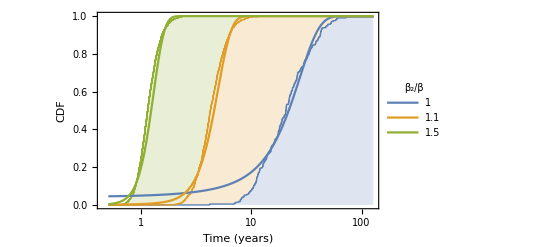

```mathematica
(*Predicted incidence curve based on normally distributed data (mean=μ, variance=v*)
f[t_,μ_,v_]:=0.5(1+Erf[(t-μ)/(Sqrt[v] √2)])
Show[
ListLogLinearPlot[incidenceCurveList,Joined->True,PlotRange->All,PlotStyle->Thin,Filling->{1->Bottom,2->{1},3->{2}}],
LogLinearPlot[Evaluate[Table[f[t,mean[[i]],var[[i]] ],{i,1,Length[mean]}]],{t,tMin,tMax},PlotRange->All,
PlotLegends->Placed[LineLegend[Map[(1+ϵ)/.#&,params],LegendLabel->"β_2/β",LabelStyle->Directive[18,FontFamily->font,GrayLevel[0.4]],LegendFunction->"Frame",Background->White],Scaled[{0.85,0.35}]]],
(*LogLinearPlot[Evaluate[Table[1-Exp[-t/mean[[i]]],{i,1,Length[mean]}]],{t,0.001,Max[timeData]},PlotStyle->Dotted,PlotRange->All]*)
Frame->True,
FrameTicksStyle->Directive[ticksSize,FontFamily->font],
FrameLabel->{Style["Time (years)",labelSize,FontFamily->font],Style["CDF",labelSize,FontFamily->font]},

(*FrameTicks->{{Automatic,Automatic},{Table[{i/Log10[ⅇ],ToString[N[100 10^i]]<>"%"(*Superscript["10",i]*)},{i,-4,0}],Table[{i/Log10[ⅇ],""},{i,-4,0}]}},
*)
ImageSize->400
]/.myPlotStyle
```

## 4. Clonal dominance in man

## Functions

### Parameter defintions

```mathematica
paramFunc[§𝒩_,§ℓ_,§β_,§ϵ_]:={𝒩->§𝒩,sStar->§sStar,nStar->§nStar,𝒮->1,β->§β,ℓ->§ℓ,δ->(§β §nStar)/(§sStar),d->(§sStar)/(§ℓ §nStar)-§β,a->(1/(§ℓ)-(§β §nStar)/(§sStar))(§𝒩)/(§𝒩-§nStar),ϵ->§ϵ,γβ->1,γδ->0,γd->0,γa->0}/.{§sStar->0.01§𝒩,§nStar->0.99§𝒩}
```

### Analytical results

```mathematica
getZ0[params_]:=Module[{z0},
z0=(a(𝒩-nStar)/𝒩)/(δ+a(𝒩-nStar)/𝒩)1/𝒩/.params;
Return[z0];
]
```

```mathematica
conditionalProb[z0_,σ_,params_]:=Module[{§ϵ,§𝒩,ξ,𝒜,ℬ,Λ,prob},
§ϵ=ϵ/.params;
§𝒩=𝒩/.params;
ξ=(nStar/𝒩)/.params;
𝒜=((β(sStar-β ℓ nStar)𝒩)/((sStar+(1-β ℓ)nStar)sStar)(γβ-γδ-γd+γa))/.params;
ℬ=((β(sStar-β ℓ nStar)nStar 𝒩)/((sStar+(1-β ℓ)nStar)^2 sStar))/.params;
Λ=(§ϵ §𝒩 𝒜)/ℬ;

If[§ϵ==0,
(*Neutral process*)
prob=z0/(σ ξ),
(*Selective process*)
prob=((1-Exp[-Λ z0])/(1-Exp[-Λ σ ξ]))
];
Return[prob];
]
```

```mathematica
conditionalTime[z0_,σ_,params_]:=Module[{§ϵ,§𝒩,ξ,𝒜,ℬ,Λ,time},
§ϵ=ϵ/.params;
§𝒩=𝒩/.params;
ξ=(nStar/𝒩)/.params;
𝒜=((β(sStar-β ℓ nStar)𝒩)/((sStar+(1-β ℓ)nStar)sStar)(γβ-γδ-γd+γa))/.params;
ℬ=((β(sStar-β ℓ nStar)nStar 𝒩)/((sStar+(1-β ℓ)nStar)^2 sStar))/.params;
Λ=(§ϵ §𝒩 𝒜)/ℬ;

If[§ϵ==0,
(*Neutral process*)
If[σ==1,
(*Fixation*)
time=(§𝒩)/ℬ(ξ-z0)/z0(Log[ξ]-Log[ξ-z0]),
(*σ-Level*)
time=(§𝒩)/ℬ(ξ-z0)/z0(Log[ξ]-Log[ξ-z0]+((1-σ)z0)/(σ(ξ-z0))Log[1-σ])
];

,(*Selective process*)
If[σ==1,
(*Fixation*)
time=(-(§𝒩)/(ℬ Λ ξ)1/((Exp[Λ z]-1) (Exp[Λ ξ]-1))((EulerGamma+Log[ξ]+Log[Λ])(1+3Exp[Λ ξ]-3Exp[Λ z]-Exp[Λ(ξ+z)])+(Log[z]-Log[ξ-z])(Exp[Λ(ξ+z)]+Exp[Λ ξ]-Exp[Λ z]-1)+( ExpIntegralEi[Λ z]-Exp[Λ ξ]ExpIntegralEi[-Λ (ξ-z)])(1-Exp[Λ ξ])+(ExpIntegralEi[-Λ z]-Exp[-Λ ξ]ExpIntegralEi[Λ (ξ-z)])(Exp[Λ z]-Exp[Λ(ξ+z)])+ExpIntegralEi[-Λ ξ](2Exp[Λ(ξ+z)]-Exp[2Λ ξ]-Exp[Λ ξ])+Exp[-Λ ξ]ExpIntegralEi[Λ ξ](Exp[Λ z]+Exp[Λ (ξ+z)]-2Exp[Λ ξ])))/.z->z0,
(*σ-Level*)
time=((§𝒩)/(ℬ Λ ξ)1/((Exp[Λ z]-1) (Exp[Λ σ ξ]-1))( 2(EulerGamma+Log[ξ]+Log[Λ])(Exp[Λ z]-Exp[Λ σ ξ])+ (Log[z]-Log[ξ-z])(1+Exp[Λ z]-Exp[Λ σ ξ]-Exp[Λ(σ ξ+z)])+ (ExpIntegralEi[Λ z]-Exp[Λ ξ] ExpIntegralEi[-Λ(ξ-z)]+Exp[Λ z]ExpIntegralEi[-Λ z]-Exp[-Λ(ξ-z)]ExpIntegralEi[Λ (ξ-z)])(Exp[Λ σ ξ]-1)+ (Exp[-Λ ξ]ExpIntegralEi[Λ ξ]+Exp[Λ ξ]ExpIntegralEi[-Λ ξ])(Exp[Λ σ ξ]-Exp[Λ z])+(Exp[-Λ(1-σ)ξ] ExpIntegralEi[Λ(1-σ)ξ]+Exp[Λ ξ]ExpIntegralEi[-Λ(1-σ)ξ]-ExpIntegralEi[Λ ξ σ]-Exp[Λ σ ξ]ExpIntegralEi[-Λ σ ξ])(Exp[Λ z]-1)+( Log[1-σ]-Log[σ])(1-Exp[Λ z]+Exp[Λ σ ξ]-Exp[Λ(σ ξ+z)])))/.z->z0
];
];

Return[time/365.25];
]
```

```mathematica
variance[z0_,σ_,params_]:=Module[{§ϵ,§𝒩,ξ,𝒜,ℬ,Λ,sec,var,sol,Δ},
§ϵ=ϵ/.params;
§𝒩=𝒩/.params;
ξ=(nStar/𝒩)/.params;
𝒜=((β(sStar-β ℓ nStar)𝒩)/((sStar+(1-β ℓ)nStar)sStar)(γβ-γδ-γd+γa))/.params;
ℬ=((β(sStar-β ℓ nStar)nStar 𝒩)/((sStar+(1-β ℓ)nStar)^2 sStar))/.params;
Λ=(§ϵ §𝒩 𝒜)/ℬ;

If[§ϵ==0,
(*Neutral process*)
If[σ==1,
(*Fixation*)
sec=(2(§𝒩)^2)/ℬ^2 ((ξ-z0)/z0 Log[(ξ-z0)/ξ]+(PolyLog[2,1]-PolyLog[2,z0/ξ])),
(*σ-Level*)
sec=(2 (§𝒩)^2)/ℬ^2 ((ξ-z0)/z0 Log[(ξ-z0)/ξ]+(PolyLog[2,σ]- PolyLog[2,z0/ξ])+(1-σ)/σ Log[1-σ] ((ξ-z0)/z0 Log[ξ/(ξ-z0)]+(1-σ)/σ Log[1-σ]-1))
];

,
(*Selective process*)
(*Requires numerical solution (here we solve the first and second moments, because we can)*)
Δ=10.^-12;(*Move away from the singular boundaries. Not perfect, but good enough*)
sol=NDSolve[{
Λ θ1'[z]+θ1''[z]==-(§𝒩)/(ℬ z(ξ-z))(1-Exp[-Λ z])/(1-Exp[-Λ σ ξ]),θ1[Δ]==0,θ1[σ(ξ-Δ)]==0,
Λ θ2'[z]+θ2''[z]==-2(§𝒩)/(ℬ z(ξ-z))θ1[z],θ2[Δ]==0,θ2[σ(ξ-Δ)]==0
},{θ1[z],θ2[z]},{z,Δ,σ(ξ-Δ)},MaxSteps->100000]//First;

sec=((θ2[z]/.sol)/((1-Exp[-Λ z])/(1-Exp[-Λ σ ξ])))/.z->z0;
];

var=sec/365.25^2-conditionalTime[z0,σ,params]^2;

Return[var];
]
```

## Plot

### Left panel: time to 4% clonality while varying N

```mathematica
(*Define parameters*)
§§ℓ=60./1440.;
§§β=1./(40.×7.);

§§σ=0.04;

𝒩Vals=Table[10.^i,{i,2,9,0.05}];
n𝒩=Length[𝒩Vals];

ϵVals={0,0.1,0.5};
nϵ=Length[ϵVals];
params=Table[Table[paramFunc[𝒩Vals[[j]],§§ℓ,§§β,ϵVals[[i]] ],{j,1,n𝒩}],{i,1,nϵ}];(*paramFunc[𝒩,ℓ,β,ϵ]*)
```

```mathematica
(*Theory predictions*)
z0Tab=Table[getZ0[params[[1,j]] ],{j,1,n𝒩}];
timePrediction=Table[Table[{𝒩/.params[[i,j]],conditionalTime[z0Tab[[j]],§§σ,params[[i,j]] ]},{j,1,n𝒩}],{i,1,nϵ}];

(*Calculate variance and export for speed*)
(*Comment out to avoid costly recalculations*)
(*analyticVariance=Table[Table[{𝒩/.params[[i,j]],conditionalTime[z0Tab[[j]],§§σ,params[[i,j]] ],variance[z0Tab[[j]],§§σ,params[[i,j]] ]},{j,1,n𝒩}],{i,1,nϵ}];
SetDirectory@NotebookDirectory[];
Map[Export["zz-data/clonal-human/variance"<>ToString[#]<>".dat",analyticVariance[[#]] ]&,Range[nϵ] ];*)
analyticVariance=Map[Import["zz-data/clonal-human/variance"<>ToString[#]<>".dat"]&,Range[nϵ] ];
```

```mathematica
myCol=col/.myPlotStyle;
linePlot=Show[
ListLogLinearPlot[Table[timePrediction[[j]],{j,1,Length[ϵVals]}],Joined->True,PlotStyle->myCol,
PlotLegends->Placed[LineLegend[Table[NumberForm[1+ϵVals[[i]],{2,1}],{i,1,Length[ϵVals]}],LegendLabel->"β_2/β",LabelStyle->Directive[ticksSize,FontFamily->font,GrayLevel[0.4] ],LegendFunction->"Frame",LegendMarkerSize->20,Spacings->{0.5,0.3},Background->White],Scaled[{0.9,0.73}] ] 
],

Table[
ListLogLinearPlot[{
Table[{analyticVariance[[i,j,1]],analyticVariance[[i,j,2]]-Sqrt[analyticVariance[[i,j,3]] ]},{j,1,Length[analyticVariance[[i]] ]}],
Table[{analyticVariance[[i,j,1]],analyticVariance[[i,j,2]]+Sqrt[analyticVariance[[i,j,3]] ]},{j,1,Length[analyticVariance[[i]] ]}]
},Joined->True,PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[myCol[[i]],Opacity[0.2] ] ],
{i,1,nϵ}],

PlotRange->{{2/Log10[ⅇ],9/Log10[ⅇ]},{0,90}},
PlotRangePadding->Scaled[0.02],

Frame->True,
FrameLabel->{{Style["Mean time (years)",labelSize,FontFamily->font],None},{Style["System size,  N",labelSize,FontFamily->font],None}},
FrameTicks->{{Automatic,Automatic},{Table[{x/Log10[ⅇ],Superscript["10",x]},{x,2,9}],Table[{x/Log10[ⅇ],""},{x,2,9}]}},
FrameTicksStyle->Directive[ticksSize,FontFamily->font],
(*AspectRatio->1/GoldenRatio×400/600,*)
ImageSize->400

]/.myPlotStyle
```

```mathematica
𝒩Fix={10^4,10^4,10^4,10^7,10^7};
ϵFix={1.0,1.1,1.5,1.1,1.5}-1;
paramFix=Table[paramFunc[𝒩Fix[[i]],§§ℓ,§§β, ϵFix[[i]]],{i,1,Length[𝒩Fix]}];
tRoot=Table[conditionalTime[getZ0[paramFix[[i]] ],§§σ,paramFix[[i]] ],{i,1,Length[𝒩Fix]}];
examplePlot=ListLogLinearPlot[Table[{{1,t},{𝒩,t},{𝒩,-10}}/.{t->tRoot[[i]],𝒩->𝒩Fix[[i]]},{i,1,Length[𝒩Fix]}],Joined->True,PlotStyle->Directive[Black,Dotted,Thickness[0.003] ] ];
```

```mathematica
leftPlot=Show[linePlot,examplePlot,Graphics[Text[Style["(a)",labelSize,FontFamily->font,GrayLevel[0.4],Background->White]/.myPlotStyle,Scaled[{0.05,0.93}]]] ]
```

### Right panel: time to clonality levels for to values of N

```mathematica
(*Define parameters*)
§§ℓ=60./1440.;
§§β=1./(40.×7.);

𝒩Vals={10^4,10^7};
n𝒩=Length[𝒩Vals];


ϵVals={0,0.1,0.5};
nϵ=Length[ϵVals];

params=Table[Table[paramFunc[𝒩Vals[[j]],§§ℓ,§§β,ϵVals[[i]] ],{j,1,n𝒩}],{i,1,nϵ}];

σVals=Table[10^i,{i,-3,0,0.01}];

z0Tab=Table[getZ0[params[[1,j]] ],{j,1,n𝒩}];
timePrediction=Table[Table[Table[{σ,conditionalTime[z0Tab[[j]],σ,params[[i,j]] ]},{σ,σVals}],{j,1,n𝒩}],{i,1,nϵ}];
```

```mathematica
myCol=col/.myPlotStyle;
linePlot=Show[
ListLogLinearPlot[timePrediction[[1]],Joined->True,PlotRange->{{10^-3,10^0},{0,90}},PlotStyle->Table[Directive[myCol[[1]],s],{s,{Line,Dashed}}],PlotLegends->Placed[LineLegend[Table[Directive[Black,s],{s,{Line,Dashed}}],Table[Superscript["10",Log10[𝒩] ],{𝒩,𝒩Vals}],LegendMarkerSize->20,LegendLabel->"N",LabelStyle->Directive[ticksSize,FontFamily->font,GrayLevel[0.4]],LegendFunction->"Frame",Spacings->{0.5,0.3},Background->White(*,LegendLayout->"Row"*)],Scaled[{0.7,0.77}]]],

ListLogLinearPlot[timePrediction[[2]],Joined->True,PlotRange->{{10^-3,10^0},{0,90}},PlotStyle->Table[Directive[myCol[[2]],s],{s,{Line,Dashed}}] ],
ListLogLinearPlot[timePrediction[[3]],Joined->True,PlotRange->{{10^-3,10^0},{0,90}},PlotStyle->Table[Directive[myCol[[3]],s],{s,{Line,Dashed}}] ],

PlotRangePadding->{0.1,0.3},
Frame->True,
FrameTicksStyle->Directive[ticksSize,FontFamily->font],
FrameLabel->{Style["Level of clonality",labelSize,FontFamily->font],Style["Mean time (years)",labelSize,FontFamily->font]},

FrameTicks->{{Automatic,Automatic},{Table[{i/Log10[ⅇ],ToString[N[100 10^i]]<>"%"(*Superscript["10",i]*)},{i,-4,0}],Table[{i/Log10[ⅇ],""},{i,-4,0}]}},

ImageSize->400
]/.myPlotStyle;
```

```mathematica
rightPlot=Show[linePlot,Graphics[Text[Style["(b)",labelSize,FontFamily->font,GrayLevel[0.4],Background->White]/.myPlotStyle,Scaled[{0.05,0.93}]]] ]
```

### Combine left and right panels

```mathematica
Row[{
Show[leftPlot,
ImageSize->400,
ImagePadding->pad],
Show[rightPlot,
ImageSize->400,
ImagePadding->pad]
}]/.{pad->{{47,16},{50,5}}}
```

### Left panel: time to 4% clonality while varying N

```mathematica
(*Define parameters*)
§§ℓ=60./1440.;
§§β=1./(40.×7.);

§§σ=0.04;

𝒩Vals={10^3,10^6,10^9};
n𝒩=Length[𝒩Vals];

ϵVals={0,0.1,0.5};
nϵ=Length[ϵVals];
params=Table[Table[paramFunc[𝒩Vals[[j]],§§ℓ,§§β,ϵVals[[i]] ],{j,1,n𝒩}],{i,1,nϵ}];(*paramFunc[𝒩,ℓ,β,ϵ]*)
```

```mathematica
(*Theory predictions*)
z0Tab=Table[getZ0[params[[1,j]] ],{j,1,n𝒩}];
prediction=Table[Table[{conditionalTime[z0Tab[[j]],§§σ,params[[i,j]] ],variance[z0Tab[[j]],§§σ,params[[i,j]] ]},{j,1,n𝒩}],{i,1,nϵ}];
```

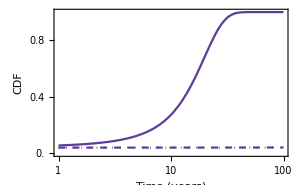
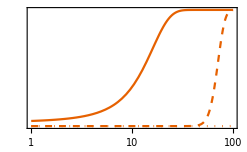
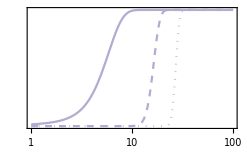
-Graphics--Graphics--Graphics--Graphics-

```mathematica
(*Predicted incidence curve based on normally distributed data (mean=μ, variance=v*)
f[t_,μ_,v_]:=0.5(1+Erf[(t-μ)/(Sqrt[v] √2)])
myCol=col/.myPlotStyle;
tMin=1;
tMax=100;
plotRange={{tMin,tMax},{0,1}};
plotRangePadding={0.22,0.04};

Row[{
LogLinearPlot[Evaluate[Table[f[t,prediction[[1,j,1]],prediction[[1,j,2]] ],{j,1,n𝒩}]],{t,tMin,tMax},PlotStyle->Table[Directive[s,myCol[[1]] ],{s,{Line,Dashed,Dotted}}],Frame->True,
PlotRange->plotRange,
PlotRangePadding->plotRangePadding,
FrameTicksStyle->Directive[ticksSize,FontFamily->font],
FrameLabel->{{Style["CDF",labelSize,FontFamily->font],None},{Style["Time (years)",labelSize,FontFamily->font],Style["β_2/β="<>ToString[1+ϵ/.params[[1,1]] ],labelSize,FontFamily->font]}},
FrameTicks->{{Table[i,{i,0.0,1.0,0.2}],Table[{i,""},{i,0.0,1.0,0.2}]},{logTicks[{1,100},True,False],logTicks[{1,100},False,False]}},
ImagePadding->{{55,2},{50,32}},
ImageSize->300],

LogLinearPlot[Evaluate[Table[f[t,prediction[[2,j,1]],prediction[[2,j,2]] ],{j,1,n𝒩}]],{t,tMin,tMax},PlotStyle->Table[Directive[s,myCol[[2]] ],{s,{Line,Dashed,Dotted}}],Frame->True,
PlotRange->plotRange,
PlotRangePadding->plotRangePadding,
FrameTicksStyle->Directive[ticksSize,FontFamily->font],
FrameLabel->{{None(*Style["CDF",labelSize,FontFamily->font]*),None},{Style["Time (years)",labelSize,FontFamily->font],Style["β_2/β="<>ToString[1+ϵ/.params[[2,1]] ],labelSize,FontFamily->font]}},
FrameTicks->{{Table[{i,""},{i,0.0,1.0,0.2}],Table[{i,""},{i,0.0,1.0,0.2}]},{logTicks[{1,100},True,False],logTicks[{1,100},False,False]}},
ImagePadding->{{2,2},{50,32}},
ImageSize->247],

LogLinearPlot[Evaluate[Table[f[t,prediction[[3,j,1]],prediction[[3,j,2]] ],{j,1,n𝒩}]],{t,tMin,tMax},PlotStyle->Table[Directive[s,myCol[[3]] ],{s,{Line,Dashed,Dotted}}],Frame->True,
PlotRange->plotRange,
PlotRangePadding->plotRangePadding,
FrameTicksStyle->Directive[ticksSize,FontFamily->font],
FrameLabel->{{None(*Style["CDF",labelSize,FontFamily->font]*),None},{Style["Time (years)",labelSize,FontFamily->font],Style["β_2/β="<>ToString[1+ϵ/.params[[3,1]] ],labelSize,FontFamily->font]}},
FrameTicks->{{Table[{i,""},{i,0.0,1.0,0.2}],Table[{i,""},{i,0.0,1.0,0.2}]},{logTicks[{1,100},True,False],logTicks[{1,100},False,False]}},
ImagePadding->{{2,2},{50,32}},
ImageSize->247],

Show[Graphics[Text[" ",{0,0}]],ImageSize->2],

LineLegend[{Directive[Black,Line],Directive[Black,Dashed],Directive[Black,Dotted]},Map[Superscript["10",Log10[#] ]&,𝒩Vals],LegendLabel->"N",LabelStyle->Directive[ticksSize,FontFamily->font,GrayLevel[0.4]],LegendFunction->"Frame",Background->White]

}]/.myPlotStyle
Clear[plotRange,plotRangePadding];
```

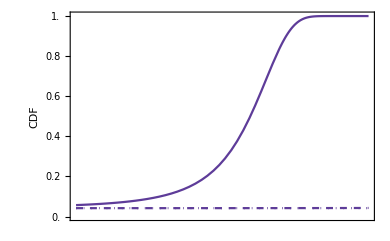
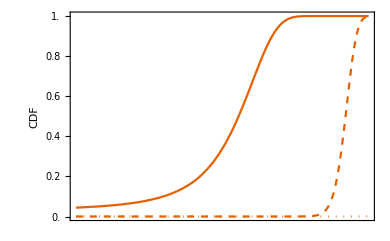
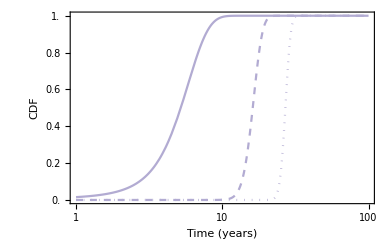
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
(*Predicted incidence curve based on normally distributed data (mean=μ, variance=v*)
f[t_,μ_,v_]:=0.5(1+Erf[(t-μ)/(Sqrt[v] √2)])
myCol=col/.myPlotStyle;
tMin=1;
tMax=100;
plotRange={{tMin,tMax},{0,1}};
plotRangePadding={0.22,0.04};

Column[{
LogLinearPlot[Evaluate[Table[f[t,prediction[[1,j,1]],prediction[[1,j,2]] ],{j,1,n𝒩}]],{t,tMin,tMax},PlotStyle->Table[Directive[s,myCol[[1]] ],{s,{Line,Dashed,Dotted}}],Frame->True,
PlotRange->plotRange,
PlotRangePadding->plotRangePadding,
FrameTicksStyle->Directive[ticksSize,FontFamily->font],
FrameLabel->{{Style["CDF",labelSize,FontFamily->font],Rotate[Style["β_2/β="<>ToString[1+ϵ/.params[[1,1]] ],labelSize,FontFamily->font],-90Degree]},{None(*Style["Time (years)",labelSize,FontFamily->font]*),None}},
FrameTicks->{{Table[{i,i},{i,0.0,1.0,0.2}],Table[{i,""},{i,0.0,1.0,0.2}]},{getTicks[{1,100},False,False],getTicks[{1,100},False,False]}},
ImagePadding->{{55,95},{2,5}},
ImageSize->390],

LogLinearPlot[Evaluate[Table[f[t,prediction[[2,j,1]],prediction[[2,j,2]] ],{j,1,n𝒩}]],{t,tMin,tMax},PlotStyle->Table[Directive[s,myCol[[2]] ],{s,{Line,Dashed,Dotted}}],Frame->True,
PlotRange->plotRange,
PlotRangePadding->plotRangePadding,
FrameTicksStyle->Directive[ticksSize,FontFamily->font],
FrameLabel->{{Style["CDF",labelSize,FontFamily->font],Rotate[Style["β_2/β="<>ToString[1+ϵ/.params[[2,1]] ],labelSize,FontFamily->font],-90Degree]},{None(*Style["Time (years)",labelSize,FontFamily->font]*),None}},
FrameTicks->{{Table[{i,i},{i,0.0,1.0,0.2}],Table[{i,""},{i,0.0,1.0,0.2}]},{getTicks[{1,100},False,False],getTicks[{1,100},False,False]}},
ImagePadding->{{55,95},{2,5}},
ImageSize->390],

LogLinearPlot[Evaluate[Table[f[t,prediction[[3,j,1]],prediction[[3,j,2]] ],{j,1,n𝒩}]],{t,tMin,tMax},PlotStyle->Table[Directive[s,myCol[[3]] ],{s,{Line,Dashed,Dotted}}],Frame->True,
PlotRange->plotRange,
PlotRangePadding->plotRangePadding,
FrameTicksStyle->Directive[ticksSize,FontFamily->font],
FrameLabel->{{Style["CDF",labelSize,FontFamily->font],Rotate[Style["β_2/β="<>ToString[1+ϵ/.params[[3,1]] ],labelSize,FontFamily->font],-90Degree]},{Style["Time (years)",labelSize,FontFamily->font],None}},
FrameTicks->{{Table[{i,i},{i,0.0,1.0,0.2}],Table[{i,""},{i,0.0,1.0,0.2}]},{getTicks[{1,100},True,False],getTicks[{1,100},False,False]}},
ImagePadding->{{55,95},{50,5}},
ImageSize->390],

Row[{
LineLegend[{Directive[Black,Line],Directive[Black,Dashed],Directive[Black,Dotted]},Map[Superscript["10",Log10[#] ]&,𝒩Vals],LegendLabel->"N",LabelStyle->Directive[ticksSize,FontFamily->font,GrayLevel[0.4]],LegendFunction->"Frame",Background->White,LegendLayout->"Row"],
Show[Graphics[Text[" ",{0,0}]],ImageSize->35]}]

},Center]/.myPlotStyle
Clear[plotRange,plotRangePadding];
```

## 5. Reconstitution of preconditioned host

## Analysis

```mathematica
fSol=First[Simplify[Solve[Evaluate[(f==(α δ)/(d+β+α δ)+d/(d+β+α δ)ψ+β/(d+β+α δ)((1-ρ)ψ f+ρ f^2))/.ρ->0],f]]]
```

```mathematica
Simplify[Solve[(ψ==δ/(δ+a)+a/(δ+a)f)/.fSol,ψ]]
```

## Functions

### Data analysis

```mathematica
getPars[form_]:=Module[{files,nFiles,i,data,parsBase,parsPars,pars},
files=FileNames[form];
nFiles=Length[files];
pars=Table[0,{i,1,nFiles}];

For[i=1,i≤nFiles,i++,
data=Import[files[[i]] ];
data=data[[1;;2]];

parsBase={§𝒩->data[[1,1]],§sStar->data[[1,2]],§nStar->data[[1,3]],§ℓ->data[[1,4]],§𝒮->1};
parsPars={§β->data[[2,1]],§δ->data[[2,2]],§a->data[[2,3]],§d->data[[2,4]],If[Length[data[[2]] ]==5,§α->data[[2,5]],§α->0]};
pars[[i]]=Flatten[{parsBase,parsPars}];
];
Return[pars];
]
```

```mathematica
getReconstProb[form_]:=Module[{files,nFiles,prob,data,ℓ,i},
files=FileNames[form];
nFiles=Length[files];

ℓ=Table[0,{i,1,nFiles}];
prob=Table[0,{i,1,nFiles}];

For[i=1,i≤nFiles,i++,
data=Import[files[[i]] ];
ℓ[[i]]=1440.×data[[1,4]];

data=Transpose[Drop[data,2] ];
prob[[i]]={ℓ[[i]],N[Mean[data[[1]] ] ]};
];
Return[prob]
]
```

```mathematica
getReconstProbAlt[form_]:=Module[{files,nFiles,prob,data,α,i},
files=FileNames[form];
nFiles=Length[files];

α=Table[0,{i,1,nFiles}];
prob=Table[0,{i,1,nFiles}];

For[i=1,i≤nFiles,i++,
data=Import[files[[i]] ];
α[[i]]= data[[2,5]];

data=Transpose[Drop[data,2] ];
prob[[i]]={α[[i]],N[Mean[data[[1]] ] ]};
];

Return[prob]
]
```

```mathematica
getReconstProbS[form_]:=Module[{files,nFiles,prob,data,sStar,i},
files=FileNames[form];
nFiles=Length[files];

sStar=Table[0,{i,1,nFiles}];
prob=Table[0,{i,1,nFiles}];

For[i=1,i≤nFiles,i++,
data=Import[files[[i]] ];
sStar[[i]]=data[[1,2]];

data=Transpose[Drop[data,2] ];
prob[[i]]={sStar[[i]],N[Mean[data[[1]] ] ]};
];
Return[prob]
]
```

### Analytical predictions

```mathematica
(*Original model: First approximation*)
reconstProb0=((1-(δ/(a+δ))^𝒮)/.{δ->(β nStar)/sStar,d->1/ℓ sStar/nStar-β,a->(1/ℓ-(β nStar)/sStar)𝒩/(𝒩-nStar)});
(*Original model: Full solution*)
reconstProb=((1-(δ/(a+δ)(d+β)/β)^𝒮)/.{δ->(β nStar)/sStar,d->1/ℓ sStar/nStar-β,a->(1/ℓ-(β nStar)/sStar)𝒩/(𝒩-nStar)});
(*Alternative model: Full solution*)
reconstProbAlt=((1-(δ/(a+δ)((β+d+α δ)+a α)/β)^𝒮)/.{δ->(β nStar)/(sStar+α nStar),d->1/ℓ sStar/nStar-β,a->(1/ℓ-(β nStar)/(sStar+α nStar))𝒩/(𝒩-nStar)});
```

## Plots

### Main panel: original model vs s^*

```mathematica
(*Load parameters and data*)
SetDirectory@NotebookDirectory[];
form[x_]:="./zz-data/preconditioned/original/engraftProb_"<>x<>".dat"
indices={"*_00_999","*_01_999","*_02_999"};
num=Length[indices];
```

```mathematica
params=Table[getPars[form[indices[[i]] ] ],{i,1,num}];
paramsSFunc=Table[{𝒩->§𝒩,𝒮->§𝒮,nStar->§nStar,sStar->§§sStar,β->§β,ℓ->§ℓ,α->§α}/.params[[i,1]],{i,1,num}];
ℓVals=Table[Round[1440.§ℓ/.params[[i,1]] ],{i,1,num}];

data=Table[getReconstProbS[form[indices[[i]] ] ],{i,1,num}];
```

```mathematica
data
```

```mathematica
myCol=col/.myPlotStyle;
mySym=Table[{(sym/.myPlotStyle)[[i,1]],(sym/.myPlotStyle)[[i,2]]×0.7},{i,1,4}];
mySymBig=Table[{(sym/.myPlotStyle)[[i,1]],(sym/.myPlotStyle)[[i,2]]×1.1},{i,1,4}];

mainPanel=Show[
LogLinearPlot[Evaluate[Table[reconstProb/.paramsSFunc[[i]],{i,1,num}] ],{§§sStar,1,128},PlotStyle->myCol,PlotRange->All,
PlotLegends->Placed[LineLegend[ℓVals,LegendMarkers->mySymBig,LegendLabel->"ℓ (mins)",LabelStyle->Directive[GrayLevel[0.4],18,FontFamily->font],LegendFunction->"Frame",Spacings->{0.5,0.3},Background->White],{0.5,0.3}] ],
LogLinearPlot[Evaluate[Table[reconstProb0/.paramsSFunc[[i]],{i,1,num}] ],{§§sStar,1,128},PlotStyle->Table[Directive[Dotted,myCol[[i]] ],{i,1,num}],PlotRange->All],
ListLogLinearPlot[data,PlotMarkers->mySymBig,PlotRange->All],

Frame->True,
FrameLabel->{Style["s^*",labelSize,FontFamily->font],Style["Reconstitution Prob.",labelSize,FontFamily->font]},
FrameTicksStyle->Directive[ticksSize,FontFamily->font],

PlotRange->{{Log10[1]/Log10[ⅇ],Log10[128]/Log10[ⅇ]},{0.92,1}},
ImageSize->350
]/.myPlotStyle
```

### Main panel: original model vs ℓ

```mathematica
(*Load parameters and data*)
SetDirectory@NotebookDirectory[];
form[x_]:="./zz-data/preconditioned/original/engraftProb_"<>x<>".dat"
indices={"00_*_001","01_*_001","02_*_001"};
num=Length[indices];

params=Table[getPars[form[indices[[i]] ] ],{i,1,num}];
paramsℓFunc=Table[{𝒩->§𝒩,𝒮->§𝒮,nStar->§nStar,sStar->§sStar,β->§β,ℓ->§§ℓ/1440.,α->§α}/.params[[i,1]],{i,1,num}];
sStarVals=Table[§sStar/.params[[i,1]],{i,1,num}];

data=Table[getReconstProb[form[indices[[i]] ] ],{i,1,num}];
```

```mathematica
myCol=col/.myPlotStyle;
mySym=Table[{(sym/.myPlotStyle)[[i,1]],(sym/.myPlotStyle)[[i,2]]×0.7},{i,1,4}];
mySymBig=Table[{(sym/.myPlotStyle)[[i,1]],(sym/.myPlotStyle)[[i,2]]×1.1},{i,1,4}];

mainPanel=Show[
Plot[Evaluate[Table[reconstProb/.paramsℓFunc[[i]],{i,1,num}] ],{§§ℓ,1,5},PlotStyle->myCol,PlotRange->All,
PlotLegends->Placed[LineLegend[sStarVals,LegendMarkers->mySymBig,LegendLabel->"s^*",LabelStyle->Directive[GrayLevel[0.4],18,FontFamily->font],LegendFunction->"Frame",Spacings->{0.5,0.3},Background->White],{0.72,0.25}] ],
Plot[Evaluate[Table[reconstProb0/.paramsℓFunc[[i]],{i,1,num}] ],{§§ℓ,1,5},PlotStyle->Table[Directive[Dotted,myCol[[i]] ],{i,1,num}],PlotRange->All],
ListPlot[data,PlotMarkers->mySym,PlotRange->All],

Frame->True,
FrameLabel->{Style["ℓ (minutes)",labelSize,FontFamily->font],Style["Reconstitution Prob.",labelSize,FontFamily->font]},
FrameTicksStyle->Directive[ticksSize,FontFamily->font],

PlotRange->{{1,5},{0.92,1}},
ImageSize->500
]/.myPlotStyle
```

```mathematica
Show[
Plot[Evaluate[Table[reconstProb/.paramsℓFunc[[i]],{i,1,num}] ],{§§ℓ,1,5},PlotStyle->myCol,PlotRange->All,
PlotLegends->Placed[LineLegend[sStarVals,LegendMarkers->mySymBig,LegendLabel->"s^*",LabelStyle->Directive[GrayLevel[0.4],18,FontFamily->font],LegendFunction->"Frame",Spacings->{0.5,0.3},Background->White],{0.15,0.3}] ],
Plot[Evaluate[Table[reconstProb0/.paramsℓFunc[[i]],{i,1,num}] ],{§§ℓ,1,5},PlotStyle->Table[Directive[Dotted,myCol[[i]] ],{i,1,num}],PlotRange->All],
ListPlot[data,PlotMarkers->mySymBig,PlotRange->All],

Frame->True,
FrameLabel->{Style["ℓ (minutes)",labelSize,FontFamily->font],Style["Reconstitution Prob.",labelSize,FontFamily->font]},
FrameTicksStyle->Directive[ticksSize,FontFamily->font],

PlotRange->{{1,5},{0.92,1}},
ImageSize->400
]/.myPlotStyle
```

### Inset: alternative model vs α (for fixed ℓ)

```mathematica
(*Load parameters and data*)
SetDirectory@NotebookDirectory[];
form[x_]:="./zz-data/preconditioned/alternative/engraftProb_"<>x<>".dat"
indices={"000_004_*_001","001_004_*_001","002_004_*_001"};
num=Length[indices];

params=Table[getPars[form[indices[[i]] ] ],{i,1,num}];
paramsℓFunc=Table[{𝒩->§𝒩,𝒮->§𝒮,nStar->§nStar,sStar->§sStar,β->§β,ℓ->§ℓ,α->§§α}/.params[[i,1]],{i,1,num}];
sStarVals=Table[§sStar/.params[[i,1]],{i,1,num}];

data=Table[getReconstProbAlt[form[indices[[i]] ] ],{i,1,num}];
```

```mathematica
myCol=col/.myPlotStyle;
mySym=Table[{(sym/.myPlotStyle)[[i,1]],(sym/.myPlotStyle)[[i,2]]×0.7},{i,1,4}];
mySymBig=Table[{(sym/.myPlotStyle)[[i,1]],(sym/.myPlotStyle)[[i,2]]×1.5},{i,1,4}];

inset=Show[
LogLinearPlot[Evaluate[Table[reconstProbAlt/.paramsℓFunc[[i]],{i,1,num}] ],{§§α,10^-8,1},PlotStyle->myCol,PlotRange->All],
ListLogLinearPlot[data,PlotMarkers->mySymBig,PlotRange->All],

Frame->True,
FrameLabel->{Style["α",labelSize-2,FontFamily->font],None},
FrameTicksStyle->Directive[ticksSize-2,FontFamily->font],
FrameTicks->{{Automatic,Automatic},{Table[{i/Log10[ⅇ],Superscript["10",i]},{i,-8,0,2}],Table[{i/Log10[ⅇ],""},{i,-8,0,2}]}},

PlotRange->{{-8/Log10[ⅇ],0/Log10[ⅇ]},{0.0,1}},
ImageSize->220,
Background->White,
ImagePadding->{{23,5},{45,3}}
]/.myPlotStyle
```

### Combined fig

```mathematica
Show[mainPanel,Epilog->Inset[inset,Scaled[{0.28,0.36}] ] ]
```

## 6. Non-preconditioned host

## Functions

### ODE integration and approximations

#### Integrators

```mathematica
solveODEs[params_,T_]:=Module[{paramSub,initialCondition,eqs,dSol},
paramSub={δ->(β nStar)/sStar,d->sStar/(ℓ nStar)-β,a->(1/ℓ-(β nStar)/sStar)𝒩/(𝒩-nStar)};

initialCondition={s1[0]==sStar,s2[0]==𝒮,n1[0]==nStar,n2[0]==0};

eqs=({
s1'[t]==(d1+β1)n1[t]-(δ1+a1(𝒩-n1[t]-n2[t])/𝒩)s1[t] ,
s2'[t]==(d2+β2)n2[t]-(δ2+a2(𝒩-n1[t]-n2[t])/𝒩)s2[t],
n1'[t]==-d1 n1[t]+a1(𝒩-n1[t]-n2[t])/𝒩 s1[t],
n2'[t]==-d2 n2[t]+a2(𝒩-n1[t]-n2[t])/𝒩 s2[t]
}/.{a1->a,d1->d,β1->β,δ1->δ,a2->a,d2->d,β2->β,δ2->δ})/.paramSub;

dSol=NDSolve[Flatten[{eqs/.params,initialCondition/.params}],{s1[t],s2[t],n1[t],n2[t]},{t,0,T}][[1]];
Return[dSol];
]
```

```mathematica
solveLinearODEs[params_,T_]:=Module[{paramSub,initialCondition,eqs,dSol},
paramSub={δ->(β nStar)/sStar,d->sStar/(ℓ nStar)-β,a->(1/ℓ-(β nStar)/sStar)𝒩/(𝒩-nStar)};

initialCondition={s2[0]==𝒮-(𝒩-nStar),n2[0]==0};

eqs=({
n2'[t]==-d(n2[t]-𝒩 s2[t]/((sStar+𝒮-(𝒩-nStar)-(β 𝒩)/δ)Exp[-δ t] +(β 𝒩)/δ)),
s2'[t]==d(n2[t]-𝒩 s2[t]/((sStar+𝒮-(𝒩-nStar)-(β 𝒩)/δ)Exp[-δ t] +(β 𝒩)/δ))+β n2[t]-δ s2[t]
})/.paramSub;

dSol=NDSolve[Flatten[{eqs/.params,initialCondition/.params}],{s2[t],n2[t]},{t,0,T}][[1]];
Return[dSol];
]
```

```mathematica
solveODEsDaily[params_,T_]:=Module[{paramSub,initialCondition,eqs,dSol,condition},
paramSub={δ->(β nStar)/sStar,d->sStar/(ℓ nStar)-β,a->(1/ℓ-(β nStar)/sStar)𝒩/(𝒩-nStar)};

initialCondition={s1[0]==sStar,s2[0]==𝒮/7.0,n1[0]==nStar,n2[0]==0};

eqs=({
s1'[t]==(d1+β1)n1[t]-(δ1+a1(𝒩-n1[t]-n2[t])/𝒩)s1[t] ,
s2'[t]==(d2+β2)n2[t]-(δ2+a2(𝒩-n1[t]-n2[t])/𝒩)s2[t],
n1'[t]==-d1 n1[t]+a1(𝒩-n1[t]-n2[t])/𝒩 s1[t],
n2'[t]==-d2 n2[t]+a2(𝒩-n1[t]-n2[t])/𝒩 s2[t]
}/.{a1->a,d1->d,β1->β,δ1->δ,a2->a,d2->d,β2->β,δ2->δ})/.paramSub;
condition=WhenEvent[Mod[t,1]==0&&t<6.5,s2[t]->(s2[t]+(𝒮/.params)/7.0)];
dSol=NDSolve[Flatten[{eqs/.params,initialCondition/.params,{condition}}],{s1[t],s2[t],n1[t],n2[t]},{t,0,T}][[1]];
Return[dSol];
]
```

#### Wrappers

```mathematica
predictionODEs[params_]:=Module[{dSol,x,T=10},
dSol=solveODEs[params,T];
x=((n2[t]/.dSol)/.t->T)/(nStar/.params);
Return[x];
]
```

```mathematica
predictionSmall[params_]:=Module[{paramSub,x},
paramSub={δ->(β nStar)/sStar,d->sStar/(ℓ nStar)-β,a->(1/ℓ-(β nStar)/sStar)𝒩/(𝒩-nStar)};
x=((1/nStar(a(𝒩-nStar)/𝒩)/(δ+a(𝒩-nStar)/𝒩)𝒮)/.paramSub)/.params;
x=Min[x,1];
Return[x];
]
```

```mathematica
predictionBig[params_]:=Module[{dSol,x,T=10},
dSol=solveLinearODEs[params,T];
x=((n2[t]/.dSol)/.t->T)/(nStar/.params);
x=Min[Max[x,0],1];
Return[x];
]
```

### Data Analysis

```mathematica
getPars[dir_]:=Module[{files,nFiles,i,data,parsBase,parsPars,parsSel,pars},
files=FileNames["*.dat",dir];
nFiles=Length[files];
pars=Table[0,{i,1,nFiles}];

For[i=1,i≤nFiles,i++,
data=Import[files[[i]] ];
data=data[[1;;3]];

parsBase={𝒩->data[[1,1]],sStar->data[[1,2]],nStar->data[[1,3]],ℓ->data[[1,4]],𝒮->data[[1,5]](*,α->data[[1,6]]*)};
parsPars={β->data[[2,1]],δ->data[[2,2]],a->data[[2,3]],d->data[[2,4]]};
parsSel={γβ->data[[3,1]],γδ->data[[3,2]],γa->data[[3,3]],γd->data[[3,4]],ϵ->data[[3,5]]};

pars[[i]]=Flatten[{parsBase,parsPars,parsSel}];
];
Return[pars];
]
```

```mathematica
getData[dir_]:=Module[{files,nFiles,data,j,dose,finalState,fixProb,finalTime},
files=FileNames["*.dat",dir];

nFiles=Length[files];
dose=Table[0,{i,1,nFiles}];
finalTime=Table[0,{i,1,nFiles}];
finalState=Table[0,{i,1,nFiles}];
fixProb=Table[0,{i,1,nFiles}];


For[j=1,j≤nFiles,j++,
data=Import[files[[j]] ];
dose[[j]]=data[[1,5]];

data=Drop[data,3];
finalTime[[j]]=data[[All,1]];
finalState[[j]]=Unitize[data[[All,3]] ]; (* 1 if s2>0 or 0 if s2=0 *)
fixProb[[j]]=Mean[finalState[[j]] ];
];

Return[{dose,finalTime,finalState,fixProb}];
]
```

```mathematica
extractFixationStats[dir_]:=Module[{fixProb,meanUnconditional,stdUnconditional,meanConditional,stdConditional,dose,time,state,prob},
{dose,time,state,prob}=getData[dir];

fixProb=Table[{dose[[i]],N[prob[[i]] ]},{i,1,Length[dose]}];
meanUnconditional=Table[{dose[[i]],Mean[time[[i]] ]/365.25},{i,1,Length[dose]}];
stdUnconditional=Table[{dose[[i]],StandardDeviation[time[[i]] ]/365.25},{i,1,Length[dose]}];

meanConditional=Table[{dose[[i]],Mean[time[[i,Flatten[Position[state[[i]],1]] ]]]/365.25},{i,1,Length[dose]}];
stdConditional=Table[{dose[[i]],StandardDeviation[time[[i,Flatten[Position[state[[i]],1]] ]]]/365.25},{i,1,Length[dose]}];

Return[{fixProb,meanUnconditional,stdUnconditional,meanConditional,stdConditional}];
]
```

### Analytical formulae

```mathematica
getZ0[params_]:=Module[{dSol,T=10,z0},
dSol=solveODEs[params,T];
z0=((n2[t]/.dSol)/.t->T)/(𝒩/.params);
Return[z0];
]
```

```mathematica
conditionalProb[z0_,σ_,params_]:=Module[{§ϵ,§𝒩,ξ,𝒜,ℬ,Λ,prob},
§ϵ=ϵ/.params;
§𝒩=𝒩/.params;
ξ=(nStar/𝒩)/.params;
𝒜=((β(sStar-β ℓ nStar)𝒩)/((sStar+(1-β ℓ)nStar)sStar)(γβ-γδ-γd+γa))/.params;
ℬ=((β(sStar-β ℓ nStar)nStar 𝒩)/((sStar+(1-β ℓ)nStar)^2 sStar))/.params;
Λ=(§ϵ §𝒩 𝒜)/ℬ;

If[§ϵ==0,
(*Neutral process*)
prob=z0/(σ ξ),
(*Selective process*)
prob=((1-Exp[-Λ z0])/(1-Exp[-Λ σ ξ]))
];
Return[prob];
]
```

```mathematica
conditionalTime[z0_,σ_,params_]:=Module[{§ϵ,§𝒩,ξ,𝒜,ℬ,Λ,time},
§ϵ=ϵ/.params;
§𝒩=𝒩/.params;
ξ=(nStar/𝒩)/.params;
𝒜=((β(sStar-β ℓ nStar)𝒩)/((sStar+(1-β ℓ)nStar)sStar)(γβ-γδ-γd+γa))/.params;
ℬ=((β(sStar-β ℓ nStar)nStar 𝒩)/((sStar+(1-β ℓ)nStar)^2 sStar))/.params;
Λ=(§ϵ §𝒩 𝒜)/ℬ;

If[§ϵ==0,
(*Neutral process*)
If[σ==1,
(*Fixation*)
time=(§𝒩)/ℬ(ξ-z0)/z0(Log[ξ]-Log[ξ-z0]),
(*σ-Level*)
time=(§𝒩)/ℬ(ξ-z0)/z0(Log[ξ]-Log[ξ-z0]+((1-σ)z0)/(σ(ξ-z0))Log[1-σ])
];

,(*Selective process*)
If[σ==1,
(*Fixation*)
time=(-(§𝒩)/(ℬ Λ ξ)1/((Exp[Λ z]-1) (Exp[Λ ξ]-1))((EulerGamma+Log[ξ]+Log[Λ])(1+3Exp[Λ ξ]-3Exp[Λ z]-Exp[Λ(ξ+z)])+(Log[z]-Log[ξ-z])(Exp[Λ(ξ+z)]+Exp[Λ ξ]-Exp[Λ z]-1)+( ExpIntegralEi[Λ z]-Exp[Λ ξ]ExpIntegralEi[-Λ (ξ-z)])(1-Exp[Λ ξ])+(ExpIntegralEi[-Λ z]-Exp[-Λ ξ]ExpIntegralEi[Λ (ξ-z)])(Exp[Λ z]-Exp[Λ(ξ+z)])+ExpIntegralEi[-Λ ξ](2Exp[Λ(ξ+z)]-Exp[2Λ ξ]-Exp[Λ ξ])+Exp[-Λ ξ]ExpIntegralEi[Λ ξ](Exp[Λ z]+Exp[Λ (ξ+z)]-2Exp[Λ ξ])))/.z->z0,
(*σ-Level*)
time=((§𝒩)/(ℬ Λ ξ)1/((Exp[Λ z]-1) (Exp[Λ σ ξ]-1))( 2(EulerGamma+Log[ξ]+Log[Λ])(Exp[Λ z]-Exp[Λ σ ξ])+ (Log[z]-Log[ξ-z])(1+Exp[Λ z]-Exp[Λ σ ξ]-Exp[Λ(σ ξ+z)])+ (ExpIntegralEi[Λ z]-Exp[Λ ξ] ExpIntegralEi[-Λ(ξ-z)]+Exp[Λ z]ExpIntegralEi[-Λ z]-Exp[-Λ(ξ-z)]ExpIntegralEi[Λ (ξ-z)])(Exp[Λ σ ξ]-1)+ (Exp[-Λ ξ]ExpIntegralEi[Λ ξ]+Exp[Λ ξ]ExpIntegralEi[-Λ ξ])(Exp[Λ σ ξ]-Exp[Λ z])+(Exp[-Λ(1-σ)ξ] ExpIntegralEi[Λ(1-σ)ξ]+Exp[Λ ξ]ExpIntegralEi[-Λ(1-σ)ξ]-ExpIntegralEi[Λ ξ σ]-Exp[Λ σ ξ]ExpIntegralEi[-Λ σ ξ])(Exp[Λ z]-1)+( Log[1-σ]-Log[σ])(1-Exp[Λ z]+Exp[Λ σ ξ]-Exp[Λ(σ ξ+z)])))/.z->z0
];
];

Return[time/365.25];
]
```

```mathematica
variance[z0_,σ_,params_]:=Module[{§ϵ,§𝒩,ξ,𝒜,ℬ,Λ,sec,var,sol,Δ},
§ϵ=ϵ/.params;
§𝒩=𝒩/.params;
ξ=(nStar/𝒩)/.params;
𝒜=((β(sStar-β ℓ nStar)𝒩)/((sStar+(1-β ℓ)nStar)sStar)(γβ-γδ-γd+γa))/.params;
ℬ=((β(sStar-β ℓ nStar)nStar 𝒩)/((sStar+(1-β ℓ)nStar)^2 sStar))/.params;
Λ=(§ϵ §𝒩 𝒜)/ℬ;

If[§ϵ==0,
(*Neutral process*)
If[σ==1,
(*Fixation*)
sec=(2(§𝒩)^2)/ℬ^2 ((ξ-z0)/z0 Log[(ξ-z0)/ξ]+(PolyLog[2,1]-PolyLog[2,z0/ξ])),
(*σ-Level*)
sec=(2 (§𝒩)^2)/ℬ^2 ((ξ-z0)/z0 Log[(ξ-z0)/ξ]+(PolyLog[2,σ]- PolyLog[2,z0/ξ])+(1-σ)/σ Log[1-σ] ((ξ-z0)/z0 Log[ξ/(ξ-z0)]+(1-σ)/σ Log[1-σ]-1))
];

,
(*Selective process*)
(*Requires numerical solution (here we solve the first and second moments, because we can)*)
Δ=10.^-10;(*Move away from the singular boundaries. Not perfect, but good enough*)
sol=NDSolve[{
Λ θ1'[z]+θ1''[z]==-(§𝒩)/(ℬ z(ξ-z))(1-Exp[-Λ z])/(1-Exp[-Λ σ ξ]),θ1[Δ]==0,θ1[σ(ξ-Δ)]==0,
Λ θ2'[z]+θ2''[z]==-2(§𝒩)/(ℬ z(ξ-z))θ1[z],θ2[Δ]==0,θ2[σ(ξ-Δ)]==0
},{θ1[z],θ2[z]},{z,Δ,σ(ξ-Δ)},MaxSteps->100000]//First;

sec=((θ2[z]/.sol)/((1-Exp[-Λ z])/(1-Exp[-Λ σ ξ])))/.z->z0;
];

var=sec/365.25^2-conditionalTime[z0,σ,params]^2;

Return[var];
]
```

### Plotting

```mathematica
chimerismErrorPlot[{odePrediction_,smallPrediction_,bigPrediction_},{smallError_,bigError_},params_,label_,legend_]:=Module[{myCol,mySym,mySymLegend,mySymError,myTicks,myTicksError,predPlot,errorPlot,plot,imageSize=370},

myCol=col/.myPlotStyle;
mySym=Table[{(sym/.myPlotStyle)[[j,1]],(sym/.myPlotStyle)[[j,2]]×1.3},{j,1,4}];
mySymLegend=Table[{(sym/.myPlotStyle)[[j,1]],(sym/.myPlotStyle)[[j,2]]×1.0},{j,1,4}];
mySymError=Table[{(sym/.myPlotStyle)[[j,1]],(sym/.myPlotStyle)[[j,2]]×2.2},{j,1,4}];

myTicks={{Table[{j/Log10[ⅇ],Superscript["10",j]},{j,-4,0}],Table[{j/Log10[ⅇ],""},{j,-4,0}]},{Table[{j/Log10[ⅇ],""(*Superscript["10",i]*)},{j,0,5}],Table[{j/Log10[ⅇ],""},{j,0,5}]}};
myTicksError={{Automatic,Automatic},{Table[{j/Log10[ⅇ],Superscript["10",j]},{j,0,5}],Table[{j/Log10[ⅇ],""},{j,0,5}]}};
predPlot=Show[
ListLogLogPlot[smallPrediction,Joined->True,PlotStyle->myCol],
ListLogLogPlot[bigPrediction,Joined->True,PlotStyle->myCol],

If[legend==True,
ListLogLogPlot[odePrediction,PlotMarkers->mySym,PlotLegends->Placed[LineLegend[Round[1440ℓVals],LegendMarkers->mySymLegend,LegendLabel->"ℓ",LabelStyle->Directive[GrayLevel[0.4],ticksSize,FontFamily->font],LegendFunction->"Frame",Spacings->{0.3,0.5},Background->White],{0.08,0.55}]],
ListLogLogPlot[odePrediction,PlotMarkers->mySym]
],

PlotRange->1/Log10[ⅇ]{{0,5},{-4.1,0}},
Frame->True,
FrameTicksStyle->Directive[ticksSize,FontFamily->font],
FrameTicks->myTicks,


ImageSize->imageSize,AspectRatio->0.5,
ImagePadding->{{35,5},{0(*25*),5}}
]/.myPlotStyle;

predPlot=Show[predPlot,
Graphics[Text[Style[label,labelSize,FontFamily->font,GrayLevel[0.4],Background->White]/.myPlotStyle,Scaled[{0.05,0.93}]]],
Graphics[Text[Style["s^*="<>ToString[sStar/.params[[1,1]] ],labelSize,FontFamily->font,GrayLevel[0.4],Background->White]/.myPlotStyle,Scaled[{0.5,0.93}]]]
];

errorPlot=Show[
ListLogLinearPlot[smallError,PlotMarkers->mySymError],
ListLogLinearPlot[bigError,PlotMarkers->mySymError],

PlotRange->{{0,5/Log10[ⅇ]},{-1.2,1.2}},
Frame->True,
FrameTicksStyle->Directive[ticksSize,FontFamily->font],
FrameTicks->myTicksError,
FrameLabel->{{None,None},{Style["𝒮",labelSize,FontFamily->font],None}},


ImageSize->imageSize,AspectRatio->0.3,
ImagePadding->{{35,5},{50,0}}
]/.myPlotStyle;

plot=Column[{predPlot,errorPlot},Spacings->0];
Return[plot];
]
```

```mathematica
multipleDosesPlot[singleBolus_,dailyInjections_,params_,T_]:=Module[{𝒮Vals,n𝒮,myCol,max,plot},
𝒮Vals=𝒮/.params;
n𝒮=Length[𝒮Vals];

myCol=col/.myPlotStyle;

(*max=Max[Table[(n2[t]/.dailyInjections[[j]])/.t->T,{j,1,nS}] ];
max=Ceiling[xxx,10^Floor[Log10[xxx]]]/.xxx->max;*)
max=2000;

plot=Show[
Plot[Evaluate[Table[n2[t]/.singleBolus[[j]],{j,1,n𝒮}] ],{t,0,T},PlotStyle->Table[Directive[myCol[[j]],Opacity[0.8],Thick,Dashed],{j,1,nS}] ],
Plot[Evaluate[Table[n2[t]/.dailyInjections[[j]],{j,1,n𝒮}] ],{t,0,T},PlotStyle->myCol,PlotLegends->Placed[LineLegend[𝒮Vals,LegendLabel->"𝒮",LabelStyle->Directive[labelSize-2,FontFamily->font,GrayLevel[0.4] ],LegendFunction->"Frame",Spacings->{0.5,0.3},Background->White],Scaled[{0.16,0.65}] ] ],


PlotRange->{{0,T},{0,max}},
PlotRangePadding->0.05,

Frame->True,
FrameLabel->{{Style["n_2",labelSize,FontFamily->font],None},{Style["Time (days)",labelSize,FontFamily->font],None}},
FrameTicksStyle->Directive[ticksSize,FontFamily->font],

ImageSize->500,
Background->White,
ImagePadding->{{62,10},{48,10}},
AspectRatio->0.45
]/.myPlotStyle;

Return[plot];
]
```

```mathematica
errorLogLinearPlot[x_,σ_,col_]:=Module[{(*Δ=0,*)num,points,lines,(*bars,*)plot},
num=Length[x];

points=ListLogLinearPlot[x,PlotStyle->col];
lines=ListLogLinearPlot[Table[{{x[[i,1]],Max[x[[i,2]]-σ[[i,2]],0]},{x[[i,1]],x[[i,2]]+σ[[i,2]]}},{i,1,num}],PlotStyle->Directive[col,Thickness[0.004]],PlotMarkers->None,Joined->True];
(*bars=
Table[
Graphics[{
{col,Line[{{x[[i,1]]-Δ,Max[x[[i,2]]-σ[[i,2]],0]},{x[[i,1]]+Δ,Max[x[[i,2]]-σ[[i,2]],0]}}]},
{col,Line[{{x[[i,1]]-Δ,x[[i,2]]+σ[[i,2]]},{x[[i,1]]+Δ,x[[i,2]]+σ[[i,2]]}}]}
}],
{i,1,num}];*)

plot=Show[lines,(*bars,*)points];

Return[plot];
]
```

## Initial chimerism

```mathematica
(*Initiate variable parameters*)
𝒮Vals=Table[10^i,{i,0,5,1/3}];(*This is my x-axis variable; dose size*)
n𝒮=Length[𝒮Vals];

sStarVals={10,100};
nS=Length[sStarVals];

ℓVals={1.,3.,5.}/1440.;
nℓ=Length[ℓVals];
```

```mathematica
paramsFunc[§sStar_,§ℓ_,§𝒮_]:={𝒩->10000,sStar->§sStar,nStar->9900,β->1./39,𝒮->§𝒮,ℓ->§ℓ};
paramsTab=Table[Table[Table[paramsFunc[sStarVals[[i]],ℓVals[[j]],𝒮Vals[[k]] ],{k,1,n𝒮}],{j,1,nℓ}],{i,1,nS}];
```

```mathematica
(*Get chimerism predictions*)
endSmall=Ceiling[(n𝒮+4)/2];
startBig=Floor[(n𝒮-4)/2]+2;
odePrediction=Table[Table[Table[{𝒮/.paramsTab[[i,j,k]],predictionODEs[paramsTab[[i,j,k]] ]},{k,1,n𝒮}],{j,1,nℓ}],{i,1,nS}];
smallPrediction=Table[Table[Table[{𝒮/.paramsTab[[i,j,k]],predictionSmall[paramsTab[[i,j,k]] ]},{k,1,endSmall}],{j,1,nℓ}],{i,1,nS}];
bigPrediction=Table[Table[Table[{𝒮/.paramsTab[[i,j,k]],predictionBig[paramsTab[[i,j,k]] ]},{k,startBig,n𝒮}],{j,1,nℓ}],{i,1,nS}];
```

```mathematica
(*Calculate errors*)
smallError=Table[Table[Table[{𝒮/.paramsTab[[i,j,k]],(smallPrediction[[i,j,k,2]]-odePrediction[[i,j,k,2]])/odePrediction[[i,j,k,2]]},{k,1,endSmall}],{j,1,nℓ}],{i,1,nS}];bigError=Table[Table[Table[{𝒮/.paramsTab[[i,j,k]],(bigPrediction[[i,j,k-startBig+1,2]]-odePrediction[[i,j,k,2]])/odePrediction[[i,j,k,2]]},{k,startBig,n𝒮}],{j,1,nℓ}],{i,1,nS}];
```

```mathematica
plot10=chimerismErrorPlot[{odePrediction[[1]],smallPrediction[[1]],bigPrediction[[1]]},{smallError[[1]],bigError[[1]]},paramsTab[[1]],"(a)",False];
plot100=chimerismErrorPlot[{odePrediction[[2]],smallPrediction[[2]],bigPrediction[[2]]},{smallError[[2]],bigError[[2]]},paramsTab[[2]],"(b)",True];
```

```mathematica
(*Plot*)
Row[{
Show[Graphics[Text[Rotate[Style["  Error         Chimerism",labelSize,FontFamily->font,GrayLevel[0.4]]/.myPlotStyle,90Degree],{0,0}]],ImageSize->{24,250}],
plot10,
plot100
}," "]
```

## Multiple doses

```mathematica
(*Parameters*)
𝒮Vals={98,980,2100};
n𝒮=Length[𝒮Vals];

T=7;
paramsFunc[§𝒮_]:={𝒩->10000,sStar->100,nStar->9900,β->1./39,𝒮->§𝒮,ℓ->3./1440.};
paramsTab=Table[paramsFunc[𝒮Vals[[i]] ],{i,1,n𝒮}];
```

```mathematica
(*Integrate ODEs*)
singleBolus=Table[solveODEs[paramsTab[[i]],T],{i,1,n𝒮}];
dailyInjections=Table[solveODEsDaily[paramsTab[[i]],T],{i,1,n𝒮}];
```

```mathematica
(*Plot*)
multipleDosesPlot[singleBolus,dailyInjections,paramsTab,T]
```

## Takeover probability and time

### Analyse Data

```mathematica
(*Load parameters and data*)
SetDirectory@NotebookDirectory[];
dirs={"./zz-data/non-preconditioned/fixation-epsilon_01/","./zz-data/non-preconditioned/fixation-epsilon_05/"};
nϵ=Length[dirs];

params=Table[getPars[dirs[[i]] ],{i,1,nϵ}];
n𝒮=Length[params[[1]] ];

data=Table[extractFixationStats[dirs[[i]] ],{i,1,nϵ}];
dataProb=Table[data[[i,1]],{i,1,nϵ}];
dataTime=Table[data[[i,4]],{i,1,nϵ}];
dataTimeSigma=Table[data[[i,5]],{i,1,nϵ}];
```

### Analytic predictions

```mathematica
𝒮Vals=Table[2^j,{j,0,13,0.1}];
n𝒮=Length[𝒮Vals];
moreParams=Table[Table[Append[Drop[params[[i,1]],{5}],𝒮->𝒮Vals[[j]] ],{j,1,n𝒮}],{i,1,nϵ}];

z0=Table[Table[getZ0[moreParams[[i,j]] ],{j,1,n𝒮}],{i,1,nϵ}];
analyticProb=Table[Table[{𝒮/.moreParams[[i,j]],conditionalProb[z0[[i,j]],1,moreParams[[i,j]] ]},{j,1,n𝒮}],{i,1,nϵ}];
analyticTime=Table[Table[{𝒮/.moreParams[[i,j]],conditionalTime[z0[[i,j]],1,moreParams[[i,j]] ]},{j,1,n𝒮}],{i,1,nϵ}];

(*Calculate variance and export for speed*)
(*Comment out to avoid costly recalculations*)
(*analyticVariance=Table[Table[{𝒮/.moreParams[[i,j]],conditionalTime[z0[[i,j]],1,moreParams[[i,j]] ],variance[z0[[i,j]],1,moreParams[[i,j]] ]},{j,1,n𝒮}],{i,1,nϵ}];
Map[Export["zz-data/non-preconditioned/variance"<>ToString[#]<>".dat",analyticVariance[[#]] ]&,Range[nϵ] ];*)

analyticVariance=Map[Import["zz-data/non-preconditioned/variance"<>ToString[#]<>".dat"]&,Range[nϵ] ];
```

### Plot fixation probability

```mathematica
myCol=col/.myPlotStyle;
probPlot=Show[
ListLogLinearPlot[Table[dataProb[[i]],{i,1,nϵ}],PlotStyle->myCol[[2;;3]] ],
ListLogLinearPlot[analyticProb,Joined->True,PlotRange->All,PlotStyle->{Directive[myCol[[2]],Line],Directive[myCol[[3]],Dashed]},PlotRange->All,PlotLegends->Placed[LineLegend[Table[(1+ϵ)/.params[[i,1]],{i,1,nϵ}],LegendMarkerSize->20,LegendLabel->"β_2/β",LabelStyle->Directive[18,FontFamily->font,GrayLevel[0.4]],LegendFunction->"Frame",Background->White],Scaled[{0.85,0.32}]]],
PlotRange->{{0/Log10[ⅇ],4/Log10[ⅇ]},{0,1}},
PlotRangePadding->{0.2,0.04},
AxesOrigin->Automatic,

Frame->True,
FrameLabel->{{Style["Fixation prob.",labelSize,FontFamily->font],None},{None(*Style["𝒮",labelSize,FontFamily->font]*),None}},
FrameTicksStyle->Directive[ticksSize,FontFamily->font],
FrameTicks->{{Automatic,Automatic},{Table[{i/Log10[ⅇ],Superscript["10",i]},{i,0,4}],Table[{i/Log10[ⅇ],""},{i,0,4}]}},

ImagePadding->{{55,5},{55-30,5}},
ImageSize->350
]/.myPlotStyle;

topPlot=Show[probPlot,Graphics[Text[Style["(a)",labelSize,FontFamily->font,GrayLevel[0.4],Background->White]/.myPlotStyle,Scaled[{0.05,0.93}]]] ]
```

### Plot fixation time

```mathematica
myCol=col/.myPlotStyle;
timePlot=Show[
Table[errorLogLinearPlot[dataTime[[i]],dataTimeSigma[[i]],myCol[[i+1]] ],{i,1,nϵ}],
ListLogLinearPlot[analyticTime,Joined->True,PlotStyle->{Directive[myCol[[2]],Line],Directive[myCol[[3]],Dashed]},PlotRange->All],

Table[
ListLogLinearPlot[{
Table[{analyticVariance[[i,j,1]],analyticVariance[[i,j,2]]-Sqrt[analyticVariance[[i,j,3]] ]},{j,1,Length[analyticVariance[[i]] ]}],
Table[{analyticVariance[[i,j,1]],analyticVariance[[i,j,2]]+Sqrt[analyticVariance[[i,j,3]] ]},{j,1,Length[analyticVariance[[i]] ]}]
},Joined->True,PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[myCol[[i+1]],Opacity[0.2] ] ],
{i,1,nϵ}],

PlotRange->{{0/Log10[ⅇ],4/Log10[ⅇ]},{0,20}},
PlotRangePadding->0.2,
AxesOrigin->Automatic,

Frame->True,
FrameLabel->{{Style["Mean time (years)",labelSize,FontFamily->font],None},{Style["𝒮",labelSize,FontFamily->font],None}},
FrameTicksStyle->Directive[ticksSize,FontFamily->font],
FrameTicks->{{Automatic,Automatic},{Table[{i/Log10[ⅇ],Superscript["10",i]},{i,0,4}],Table[{i/Log10[ⅇ],""},{i,0,4}]}},

ImagePadding->{{55,5},{55,10}},
ImageSize->350
]/.myPlotStyle;

bottomPlot=Show[timePlot,Graphics[Text[Style["(b)",labelSize,FontFamily->font,GrayLevel[0.4],Background->White]/.myPlotStyle,Scaled[{0.05,0.93}]]] ]
```

### Combine plots

```mathematica
Column[{topPlot,bottomPlot},Spacings->0]
```